## Numerators

## Algebra utilities

```mathematica
SetDirectory[NotebookDirectory[]]
<<"./tools/tensTools.m"
<<"./tools/ampTools2.1.m"
```

/Users/zeno/Desktop/LTD/program/alphaLoopMisc

The documented functions in this package are: 
 ?extractTensCoeff
 ?getSymNumericCoeff

The documented functions in this package are: 
 ?contractLorentz 
 ?contractColor 
 ?contractSpin 
 ?constructLorentzProjector 
 Make sure you have the "trace_form.log" file for the gamma-algebra

gamma traces loaded

The documented functions in this package are: 
 ?contractLorentz 
 ?contractColor 
 ?contractSpin 
 ?constructLorentzProjector 
 Make sure you have the "trace_form.log" file for the gamma-algebra

gamma traces loaded

## Numerators

### LO ddbar production numerator definition

```mathematica
loNum[k_,p1_,p2_]:=(
(-I gamma[s[11],mu,s[12]])
 I vector[k,mu1]gamma[s[12],mu1,s[13]]
(-I gamma[s[13],nu,s[14]])
I vector[k-p1-p2,mu2]gamma[s[14],mu2,s[11]]
(-I  gamma[s[21],mu,s[22]])
 I vector[p1,mu6]gamma[s[22],mu6,s[23]]
(-I  gamma[s[23],nu,s[24]])
 I vector[p2,mu7]gamma[s[24],mu7,s[21]]
)

loNumerator[k_,p1_,p2_]=contractColor[contractSpin[loNum[k,p1,p2],{k,p1,p2}],i,a]/.{d->4}/.{TF->1/2}/.{Nc->3}
```

64 SP[k,p1] SP[k,p2]-32 SP[k,p2] SP[p1,p1]-32 SP[k,p1] SP[p1,p2]-32 SP[k,p2] SP[p1,p2]-32 SP[k,p1] SP[p2,p2]

### NLO Numerator definitions

#### Double Triangle

```mathematica
dtNum[k_,l_,p1_,p2_]:=(
(-I  gamma[s[11],mu,s[12]])
 I vector[k,mu1]gamma[s[12],mu1,s[13]]
(-I  gamma[s[13],mu2,s[14]] T[a[11],i[11],i[12]])
I vector[l,mu3]gamma[s[14],mu3,s[15]]
(-I  gamma[s[15],nu,s[16]])
I vector[l-p1-p2,mu4]gamma[s[16],mu4,s[17]]
(-I  gamma[s[17],mu2,s[18]] T[a[11],i[12],i[11]])
I vector[k-p1-p2,mu5]gamma[s[18],mu5,s[11]]
(-I  gamma[s[21],mu,s[22]])
 I vector[p1,mu6]gamma[s[22],mu6,s[23]]
(-I  gamma[s[23],nu,s[24]])
 I vector[p2,mu7]gamma[s[24],mu7,s[21]]
)

dtNumerator[k_,l_,p1_,p2_]=contractColor[contractSpin[dtNum[k,l,p1,p2],{k,l,p1,p2}],i,a]/.{d->4}/.{TF->1/2}/.{Nc->3}
```

1/6. Contraction completed

512 SP[k,p1] SP[k,p2] SP[l,l]-512 SP[k,l] SP[k,p2] SP[l,p1]-256 SP[k,p1] SP[k,p2] SP[l,p1]+256 SP[k,p2]^2 SP[l,p1]+256 SP[k,p2] SP[l,p1]^2-512 SP[k,l] SP[k,p1] SP[l,p2]+256 SP[k,p1]^2 SP[l,p2]-256 SP[k,p1] SP[k,p2] SP[l,p2]+512 SP[k,k] SP[l,p1] SP[l,p2]-256 SP[k,p1] SP[l,p1] SP[l,p2]-256 SP[k,p2] SP[l,p1] SP[l,p2]+256 SP[k,p1] SP[l,p2]^2+256 SP[k,l] SP[k,p2] SP[p1,p1]-256 SP[k,p2] SP[l,l] SP[p1,p1]-256 SP[k,k] SP[l,p2] SP[p1,p1]+256 SP[k,l] SP[l,p2] SP[p1,p1]+512 SP[k,p2] SP[l,p2] SP[p1,p1]+512 SP[k,l]^2 SP[p1,p2]-256 SP[k,l] SP[k,p1] SP[p1,p2]-256 SP[k,l] SP[k,p2] SP[p1,p2]-256 SP[k,k] SP[l,l] SP[p1,p2]-256 SP[k,l] SP[l,p1] SP[p1,p2]+512 SP[k,p1] SP[l,p1] SP[p1,p2]-256 SP[k,l] SP[l,p2] SP[p1,p2]+512 SP[k,p2] SP[l,p2] SP[p1,p2]-256 SP[k,l] SP[p1,p1] SP[p1,p2]+256 SP[k,l] SP[k,p1] SP[p2,p2]-256 SP[k,p1] SP[l,l] SP[p2,p2]-256 SP[k,k] SP[l,p1] SP[p2,p2]+256 SP[k,l] SP[l,p1] SP[p2,p2]+512 SP[k,p1] SP[l,p1] SP[p2,p2]-512 SP[k,l] SP[p1,p1] SP[p2,p2]-256 SP[k,l] SP[p1,p2] SP[p2,p2]

#### Double Triangle UV

D. Soper' s UV counter - term (cfr Beowulf)

```mathematica
dtNumeratorRightUV[k_,l_,p1_,p2_]=Module[{A10=4, A20=-2 ,B10=4,q0,mUV},
contractColor[contractSpin[
(ⅈ)4/3(
(-4 A20 gamma[s[24],nu,s[23]]-A10  gamma[s[24],mu4,s[23]] vector[EnergyDirection,mu4]vector[NDirection,nu])/(16 Sqrt[norm[l]^2+MUV^2]^3)
+(3A10 gamma[s[24],mu6,s[23]]vector[ls,mu6]vector[ls,nu]+3(A20+B10)MUV^2 gamma[s[24],nu,s[23]])/(16 Sqrt[norm[l]^2+MUV^2]^5)
)
(gamma[s[23],mu3,s[13]]vector[k,mu3])
(-ⅈ)gamma[s[13],mu,s[14]] 
(gamma[s[14],mu5,s[24]]vector[p1+p2-k,mu5])

(gamma[s[21],mu1,s[11]]vector[p1,mu1])
(-ⅈ) gamma[s[11],mu,s[12]]
(gamma[s[12],mu2,s[22]]vector[p2,mu2])
(-ⅈ ) gamma[s[22],nu,s[21]]

delta[i[1],i[1]],
{p1,p2,k,l,EnergyDirection,NDirection,ls}],i,a]/.{EnergyDirection->{1,0,0,0},NDirection->{1,0,0,0},ls->{0,l[[2]],l[[3]],l[[4]]}}/.{d->4}/.{TF->1/2}/.{Nc->3}];
```

Part::partd: Part specification l⟦2⟧ is longer than depth of object.

Part::partd: Part specification l⟦3⟧ is longer than depth of object.

Part::partd: Part specification l⟦4⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
dtNumeratorLeftUV[k_,l_,p1_,p2_]=Module[{A10=4, A20=-2 ,B10=4,q0,mUV},
contractColor[contractSpin[
(ⅈ)4/3(
(-4 A20 gamma[s[13],mu4,s[14]]-A10  gamma[s[13],muX1,s[14]] vector[EnergyDirection,muX1]vector[NDirection,mu4])/(16 Sqrt[norm[k]^2+MUV^2]^3)
+(3A10 gamma[s[13],muX2,s[14]]vector[ks,muX2]vector[ks,mu4]+3(A20+B10)MUV^2 gamma[s[13],mu4,s[14]])/(16 Sqrt[norm[k]^2+MUV^2]^5)
)
(gamma[s[14],mu3,s[24]]vector[l,mu3])
(-ⅈ )gamma[s[24],mu6,s[23]]
(gamma[s[23],mu5,s[13]]vector[p1+p2-l,mu5])

(gamma[s[21],mu1,s[11]]vector[p1,mu1])
(-ⅈ ) gamma[s[22],mu6,s[21]]
(gamma[s[12],mu2,s[22]]vector[p2,mu2])
(-ⅈ) gamma[s[11],mu4,s[12]]

delta[i[1],i[1]],
{p1,p2,k,l,EnergyDirection,NDirection,ks}],i,a]/.{EnergyDirection->{1,0,0,0},NDirection->{1,0,0,0},ks->{0,k[[2]],k[[3]],k[[4]]}}/.{d->4}/.{TF->1/2}/.{Nc->3}];
```

Part::partd: Part specification k⟦2⟧ is longer than depth of object.

Part::partd: Part specification k⟦3⟧ is longer than depth of object.

Part::partd: Part specification k⟦4⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

#### 2 to 2 t - channel

```mathematica
twoNum[k_,l_,p1_,p2_,p_]:=(
(-I gamma[s[11],nu,s[12]])
 I vector[k+p1+p2,mu1]gamma[s[12],mu1,s[13]]
(-I gamma[s[13],mu,s[14]])
I vector[k+p,mu3]gamma[s[14],mu3,s[15]]
(-I gamma[s[15],mu2,s[16]]T[a[11],i[11],i[12]])
I vector[k+l+p,mu4]gamma[s[16],mu4,s[17]]
(-I gamma[s[17],mu2,s[18]]T[a[11],i[12],i[11]])
I vector[k,mu5]gamma[s[18],mu5,s[11]]
(-I  gamma[s[21],mu,s[22]])
 I vector[p1,mu6]gamma[s[22],mu6,s[23]]
(-I  gamma[s[23],nu,s[24]])
 I vector[p2,mu7]gamma[s[24],mu7,s[21]]
)

twoNumerator[k_,l_,p1_,p2_,p_]=contractColor[contractSpin[twoNum[k,l,p1,p2,p],{k,l,p1,p2,p}],i,a]/.{d->4}/.{TF->1/2}/.{Nc->3}
```

-512 SP[k,k] SP[k,p1] SP[k,p2]-1024 SP[k,l] SP[k,p1] SP[k,p2]-1024 SP[k,p] SP[k,p1] SP[k,p2]-512 SP[k,p1] SP[k,p2] SP[l,p]+256 SP[k,k] SP[k,p2] SP[l,p1]+256 SP[k,p] SP[k,p2] SP[l,p1]+256 SP[k,k] SP[k,p1] SP[l,p2]+256 SP[k,p] SP[k,p1] SP[l,p2]-512 SP[k,p1] SP[k,p2] SP[p,p]-256 SP[k,l] SP[k,p2] SP[p,p1]-256 SP[k,l] SP[k,p1] SP[p,p2]-256 SP[k,k] SP[k,p2] SP[p1,p1]-512 SP[k,l] SP[k,p2] SP[p1,p1]-512 SP[k,p] SP[k,p2] SP[p1,p1]-256 SP[k,p2] SP[l,p] SP[p1,p1]+256 SP[k,k] SP[l,p2] SP[p1,p1]+256 SP[k,p] SP[l,p2] SP[p1,p1]-256 SP[k,p2] SP[p,p] SP[p1,p1]-256 SP[k,l] SP[p,p2] SP[p1,p1]-256 SP[k,k] SP[k,p1] SP[p1,p2]-512 SP[k,l] SP[k,p1] SP[p1,p2]-512 SP[k,p] SP[k,p1] SP[p1,p2]-256 SP[k,k] SP[k,p2] SP[p1,p2]-512 SP[k,l] SP[k,p2] SP[p1,p2]-512 SP[k,p] SP[k,p2] SP[p1,p2]-256 SP[k,p1] SP[l,p] SP[p1,p2]-256 SP[k,p2] SP[l,p] SP[p1,p2]+256 SP[k,k] SP[l,p1] SP[p1,p2]+256 SP[k,p] SP[l,p1] SP[p1,p2]+256 SP[k,k] SP[l,p2] SP[p1,p2]+256 SP[k,p] SP[l,p2] SP[p1,p2]-256 SP[k,p1] SP[p,p] SP[p1,p2]-256 SP[k,p2] SP[p,p] SP[p1,p2]-256 SP[k,l] SP[p,p1] SP[p1,p2]-256 SP[k,l] SP[p,p2] SP[p1,p2]-256 SP[k,k] SP[k,p1] SP[p2,p2]-512 SP[k,l] SP[k,p1] SP[p2,p2]-512 SP[k,p] SP[k,p1] SP[p2,p2]-256 SP[k,p1] SP[l,p] SP[p2,p2]+256 SP[k,k] SP[l,p1] SP[p2,p2]+256 SP[k,p] SP[l,p1] SP[p2,p2]-256 SP[k,p1] SP[p,p] SP[p2,p2]-256 SP[k,l] SP[p,p1] SP[p2,p2]

#### 2 to 2 u - channel

```mathematica
uChannelNum[k_,l_,p1_,p2_]:=(
(-I gamma[s[11],mu,s[12]])
 I vector[k+p1+p2,mu1]gamma[s[12],mu1,s[13]]
(-I gamma[s[13],mu2,s[14]])
I vector[k+l+p1+p2,mu3]gamma[s[14],mu3,s[15]]
(-I gamma[s[15],nu,s[16]])
I vector[k+l,mu4]gamma[s[16],mu4,s[17]]
(-I gamma[s[17],mu2,s[18]])
I vector[k,mu5]gamma[s[18],mu5,s[11]]
(-I  gamma[s[21],mu,s[22]])
 I vector[p1,mu6]gamma[s[22],mu6,s[23]]
(-I  gamma[s[23],nu,s[24]])
 I vector[p2,mu7]gamma[s[24],mu7,s[21]]
)

uChannelNumerator[k_,l_,p1_,p2_]=contractColor[contractSpin[uChannelNum[k,l,p1,p2],{k,l,p1,p2}],i,a]/.{d->4}/.{TF->1/2}/.{Nc->3}
```

#### 2 to 2 s - channel

```mathematica
sChannelBubNum[k_,l_,p1_,p2_]:=(
(-I gamma[s[11],nu,s[12]])
 I vector[k,mu1]gamma[s[12],mu1,s[13]]
(-I gamma[s[13],mu,s[14]])
I vector[k+p1+p2,mu3]gamma[s[14],mu3,s[15]]
(-I gamma[s[15],mu2,s[16]]T[a[11],i[11],i[12]])
I vector[k+p1+p2-l,mu4]gamma[s[16],mu4,s[17]]
(-I gamma[s[17],mu2,s[18]]T[a[11],i[12],i[11]])
I vector[k+p1+p2,mu5]gamma[s[18],mu5,s[11]]
(-I  gamma[s[21],mu,s[22]])
 I vector[p1,mu6]gamma[s[22],mu6,s[23]]
(-I  gamma[s[23],nu,s[24]])
 I vector[p2,mu7]gamma[s[24],mu7,s[21]]
)

sChannelBubNumerator[k_,l_,p1_,p2_]=contractColor[contractSpin[sChannelBubNum[k,l,p1,p2],{k,l,p1,p2}],i,a]/.{d->4}/.{TF->1/2}/.{Nc->3}
```

#### Bubble

```mathematica
bubNum[k_,l_,p1_,p2_,p_]:=(
(-I  gamma[s[11],nu,s[12]])
 I vector[k-p1-p2,mu1]gamma[s[12],mu1,s[13]]
(-I gamma[s[13],mu,s[14]])
I vector[k,mu3]gamma[s[14],mu3,s[15]]
(-I gamma[s[15],mu2,s[16]]T[a[11],i[11],i[12]])
I vector[l,mu4]gamma[s[16],mu4,s[17]]
(-I gamma[s[17],mu2,s[18]] T[a[11],i[12],i[11]])
I vector[k,mu5]gamma[s[18],mu5,s[11]]
(-I  gamma[s[21],mu,s[22]])
 I vector[p1,mu6]gamma[s[22],mu6,s[23]]
(-I  gamma[s[23],nu,s[24]])
 I vector[p2,mu7]gamma[s[24],mu7,s[21]]
)

bubNumerator[k_,l_,p1_,p2_,p_]=contractColor[contractSpin[bubNum[k,l,p1,p2,p],{k,l,p1,p2,p}],i,a]/.{d->4}/.{TF->1/2}/.{Nc->3}
```

-1024 SP[k,l] SP[k,p1] SP[k,p2]+256 SP[k,k] SP[k,p2] SP[l,p1]+256 SP[k,k] SP[k,p1] SP[l,p2]+512 SP[k,l] SP[k,p2] SP[p1,p1]-256 SP[k,k] SP[l,p2] SP[p1,p1]+512 SP[k,l] SP[k,p1] SP[p1,p2]+512 SP[k,l] SP[k,p2] SP[p1,p2]-256 SP[k,k] SP[l,p1] SP[p1,p2]-256 SP[k,k] SP[l,p2] SP[p1,p2]+512 SP[k,l] SP[k,p1] SP[p2,p2]-256 SP[k,k] SP[l,p1] SP[p2,p2]

#### 2 to 2 st - channel

```mathematica
twoV2Num[k_,l_,p1_,p2_]:=(
(-I gamma[s[11],mu,s[12]])
 I vector[k,mu1]gamma[s[12],mu1,s[13]]
(-I gamma[s[13],mu2,s[14]]T[a[11],i[11],i[12]])
I vector[l+p1+p2,mu3]gamma[s[14],mu3,s[15]]
(-I gamma[s[15],nu,s[16]])
I vector[l,mu4]gamma[s[16],mu4,s[17]]
(-I gamma[s[17],mu2,s[18]]T[a[11],i[12],i[11]])
I vector[k+p1+p2,mu5]gamma[s[18],mu5,s[11]]
(-I  gamma[s[21],mu,s[22]])
 I vector[p1,mu6]gamma[s[22],mu6,s[23]]
(-I  gamma[s[23],nu,s[24]])
 I vector[p2,mu7]gamma[s[24],mu7,s[21]]
)

twoV2Numerator[k_,l_,p1_,p2_]=contractColor[contractSpin[twoV2Num[k,l,p1,p2],{k,l,p1,p2}],i,a]/.{d->4}/.{TF->1/2}/.{Nc->3}
```

512 SP[k,p1] SP[k,p2] SP[l,l]-512 SP[k,l] SP[k,p2] SP[l,p1]+256 SP[k,p1] SP[k,p2] SP[l,p1]-256 SP[k,p2]^2 SP[l,p1]-256 SP[k,p2] SP[l,p1]^2-512 SP[k,l] SP[k,p1] SP[l,p2]-256 SP[k,p1]^2 SP[l,p2]+256 SP[k,p1] SP[k,p2] SP[l,p2]+512 SP[k,k] SP[l,p1] SP[l,p2]+256 SP[k,p1] SP[l,p1] SP[l,p2]+256 SP[k,p2] SP[l,p1] SP[l,p2]-256 SP[k,p1] SP[l,p2]^2-256 SP[k,l] SP[k,p2] SP[p1,p1]+256 SP[k,p2] SP[l,l] SP[p1,p1]+256 SP[k,k] SP[l,p2] SP[p1,p1]-256 SP[k,l] SP[l,p2] SP[p1,p1]+512 SP[k,l]^2 SP[p1,p2]+256 SP[k,l] SP[k,p1] SP[p1,p2]+256 SP[k,l] SP[k,p2] SP[p1,p2]-256 SP[k,k] SP[l,l] SP[p1,p2]+256 SP[k,l] SP[l,p1] SP[p1,p2]+256 SP[k,l] SP[l,p2] SP[p1,p2]+256 SP[k,l] SP[p1,p1] SP[p1,p2]+512 SP[k,l] SP[p1,p2]^2-256 SP[k,l] SP[k,p1] SP[p2,p2]+256 SP[k,p1] SP[l,l] SP[p2,p2]+256 SP[k,k] SP[l,p1] SP[p2,p2]-256 SP[k,l] SP[l,p1] SP[p2,p2]+256 SP[k,l] SP[p1,p2] SP[p2,p2]

### Scalar product, norm, tensor definitions

```mathematica
SP[k_,q_]:=k[[1]]q[[1]]-k[[2]]q[[2]]-k[[3]]q[[3]]-k[[4]]q[[4]]
norm[k_]:=Sqrt[k[[2]]^2+k[[3]]^2+k[[4]]^2]
vector[k_,mu_]:=k[[mu]]
g[mu_,nu_]:=-KroneckerDelta[mu,nu]+2 KroneckerDelta[mu,0]KroneckerDelta[nu,0]
```

### Tests

#### Double triangle, u - channel and st - channel equivalences

Numerators of cut diagrams obtained from the same vacuum bubble are the same up to re-routing

```mathematica
Simplify[dtNumerator[{k0,kx,ky,kz},-{l0,lx,ly,lz}-{q0,qx,qy,qz},-{q0,qx,qy,qz},1,1]-twoV2Numerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{q0,qx,qy,qz},1,1]]
```

dtNumerator[{k0,kx,ky,kz},{-l0-q0,-lx-qx,-ly-qy,-lz-qz},{-q0,-qx,-qy,-qz},1,1]-twoV2Numerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{q0,qx,qy,qz},1,1]

```mathematica
Simplify[dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{q0,qx,qy,qz},1,1]-uChannelNumerator[{k0,kx,ky,kz}-{q0,qx,qy,qz},{l0,lx,ly,lz}-{k0,kx,ky,kz},{q0,qx,qy,qz},1,1]]
```

dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{q0,qx,qy,qz},1,1]-uChannelNumerator[{k0-q0,kx-qx,ky-qy,kz-qz},{-k0+l0,-kx+lx,-ky+ly,-kz+lz},{q0,qx,qy,qz},1,1]

#### Bubble correction, s - channel and t - channel equivalences

Numerators of cut diagrams obtained from the same vacuum bubble are the same up to re - routing

```mathematica
Simplify[bubNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{0,0,0,0},{q0,qx,qy,qz},1,1]-sChannelBubNumerator[{k0,kx,ky,kz}-{q0,qx,qy,qz},-{l0,lx,ly,lz}+{k0,kx,ky,kz},{q0,qx,qy,qz},1,1]]
```

bubNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{0,0,0,0},{q0,qx,qy,qz},1,1]-sChannelBubNumerator[{k0-q0,kx-qx,ky-qy,kz-qz},{k0-l0,kx-lx,ky-ly,kz-lz},{q0,qx,qy,qz},1,1]

```mathematica
Simplify[bubNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{0,0,0,0},{q0,qx,qy,qz},1,1]-twoNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz}-{k0,kx,ky,kz},{0,0,0,0},-{q0,qx,qy,qz},1,1]]
```

bubNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{0,0,0,0},{q0,qx,qy,qz},1,1]-twoNumerator[{k0,kx,ky,kz},{-k0+l0,-kx+lx,-ky+ly,-kz+lz},{0,0,0,0},{-q0,-qx,-qy,-qz},1,1]

## LO & some testing

## Testing the flow

-Graphics-

### Flow solutions

```mathematica
tTchUsual[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=(p10+p20)/(norm[{0,kx,ky,kz}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}]-norm[{0,kx,ky,kz}-{0,lx,ly,lz}]+norm[{0,lx,ly,lz}])
```

```mathematica
tTchWeird[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=(p10+p20)/(norm[{0,kx,ky,kz}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}]+norm[{0,kx,ky,kz}])
```

One thing to remember is that for more complicated cases (not for 1 parton + q -> 2 partons), the scaling is not always ensured to be positive (or have a well - defined sign), as the denominator is a difference of norms. In this case one has to add an heaviside theta

### Dirac delta jacobians

```mathematica
usualTchDiracJ[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=Dot[Grad[norm[{0,ax,ay,az}]+norm[{0,sx,sy,sz}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}]-norm[{0,sx,sy,sz}-{0,ax,ay,az}],{sx,sy,sz,ax,ay,az}],{sx,sy,sz,ax,ay,az}]/.{sx->kx,sy->ky,sz->kz,ax->lx,ay->ly,az->lz};

weirdTchDiracJ[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=(Dot[Grad[norm[{0,sx,sy,sz}]+norm[{0,sx,sy,sz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}],{sx,sy,sz}] ,{sx,sy,sz}])/.{sx->kx,sy->ky,sz->kz,ax->lx,ay->ly,az->lz};
```

### Toy integrand

-Graphics-

```mathematica
fWeird[kx_,ky_,kz_,lx_,ly_,lz_]:=Exp[-norm[{0,kx,ky,kz}]^2-norm[{0,lx,ly,lz}]^2]/(2norm[{0,kx,ky,kz}]2norm[{0,kx,ky,kz}-{0,lx,ly,lz}](norm[{0,kx,ky,kz}]-norm[{0,lx,ly,lz}]+norm[{0,kx,ky,kz}-{0,lx,ly,lz}])(norm[{0,kx,ky,kz}]+norm[{0,lx,ly,lz}]+norm[{0,kx,ky,kz}-{0,lx,ly,lz}]))
```

-Graphics-

```mathematica
fUsual[kx_,ky_,kz_,lx_,ly_,lz_]:=Exp[-norm[{0,kx,ky,kz}]^2-norm[{0,lx,ly,lz}]^2]/(2norm[{0,lx,ly,lz}]2norm[{0,kx,ky,kz}-{0,lx,ly,lz}](norm[{0,kx,ky,kz}]+norm[{0,lx,ly,lz}]-norm[{0,kx,ky,kz}-{0,lx,ly,lz}])(-norm[{0,kx,ky,kz}]+norm[{0,lx,ly,lz}]-norm[{0,kx,ky,kz}-{0,lx,ly,lz}]))
```

### Singular structure of Toy integrand

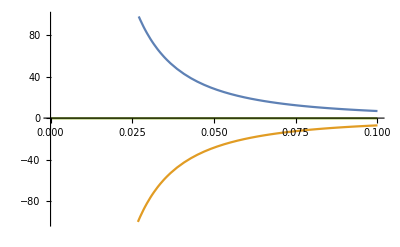

```mathematica
Plot[{fWeird[0,eps,0.5,0,0,1],fUsual[0,eps,0.5,0,0,1],fWeird[0,eps,0.5,0,0,1]+fUsual[0,eps,0.5,0,0,1]},{eps,0,0.1}]
```

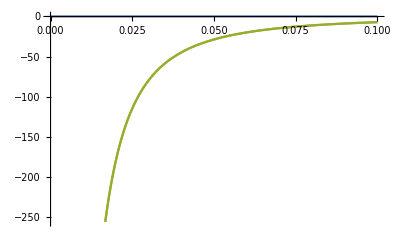

```mathematica
Plot[{fWeird[0,eps,-0.5,0,0,1],fUsual[0,eps,-0.5,0,0,1],fWeird[0,eps,-0.5,0,0,1]+fUsual[0,eps,-0.5,0,0,1]},{eps,0,0.1}]
```

### LU representation of Toy integrand

```mathematica
thF[x_]:=If[x>0,1,0];
```

```mathematica
sum[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_,sigma_]:=Module[{vt,rt,sumo},
vt=tTchUsual[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z];
rt=tTchWeird[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z];

sumo=( vt^6 thF[vt](Exp[-vt^2/sigma^2])/(usualTchDiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])fUsual[vt kx,vt ky,vt kz,vt lx,vt ly,vt lz]+rt^6 thF[rt](Exp[-rt^2/sigma^2])/(weirdTchDiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])fWeird[rt kx,rt ky,rt kz,rt lx,rt ly,rt lz]);

sumo/(Sqrt[Pi]sigma)
]
```

```mathematica
usualCutTot[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_,sigma_]:=Module[{vt,sumo},
vt=tTchUsual[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z];

sumo=vt^6 thF[vt](Exp[-vt^2/sigma^2])/(usualTchDiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])fUsual[vt kx,vt ky,vt kz,vt lx,vt ly,vt lz];

sumo/(Sqrt[Pi]sigma)
]

weirdCutTot[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_,sigma_]:=Module[{rt,sumo},
rt=tTchWeird[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z];

sumo=rt^6 thF[rt](Exp[-rt^2/sigma^2])/(weirdTchDiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])fWeird[rt kx,rt ky,rt kz,rt lx,rt ly,rt lz];

sumo/(Sqrt[Pi]sigma)
]
```

```mathematica
sum[0,0.5,1,0,0,-0.5,1,0,0,1,1,0,0,-1,0.1];
```

General::munfl: Exp[-293847.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4407.7] is too small to represent as a normalized machine number; precision may be lost.

### Cancellations of IR singularities in the Toy model

This singularity is the only one with support, and thus subject to cancellation

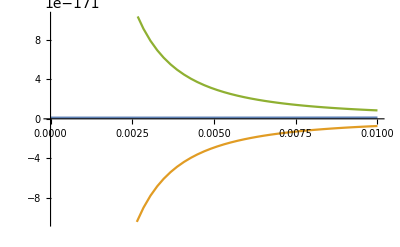

```mathematica
Plot[{sum[0,eps,0.5,0,0,1,1,0,0,1,1,0,0,-1,0.1],usualCutTot[0,eps,0.5,0,0,1,1,0,0,1,1,0,0,-1,0.1], weirdCutTot[0,eps,0.5,0,0,1,1,0,0,1,1,0,0,-1,0.1]},{eps,0,0.01}]
```

This singularity is the one without support, and actually corresponds to the limit t -> Infinity, with is suppressed exponentially by the h function

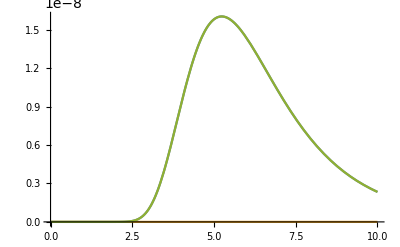

```mathematica
Plot[{sum[0,eps,1,0,0,0.5,1,0,0,1,1,0,0,-1,0.1],usualCutTot[0,eps,1,0,0,0.5,1,0,0,1,1,0,0,-1,0.1], weirdCutTot[0,eps,1,0,0,0.5,1,0,0,1,1,0,0,-1,0.1](*,1/(0.5-norm[{0,0,eps,0.5}]-norm[{0,0,eps,1}])*)},{eps,0,10}(*,PlotRange->All*)]
```

### Integration of Toy model integrand for varying h - function spread

```mathematica
(*Table[NIntegrate[sum[kx,ky,kz,lx,ly,lz,1,0,0,1,1,0,0,-1,0.2],{kx,-Infinity,Infinity},{ky,-Infinity,Infinity},{kz,-Infinity,Infinity},{lx,-Infinity,Infinity},{ly,-Infinity,Infinity},{lz,-Infinity,Infinity},Method->"AdaptiveMonteCarlo",PrecisionGoal->5,MaxPoints->10^(i),MaxRecursion->1000],{i,1,8}]*)
```

NIntegrate::maxp: The integral failed to converge after 100 integrand evaluations. NIntegrate obtained 0.17304 and 0.0619169 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 300 integrand evaluations. NIntegrate obtained 0.392086 and 0.0700208 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1100 integrand evaluations. NIntegrate obtained 0.336917 and 0.0459864 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

{0.17304,0.392086,0.336917,0.279555,0.272835,0.292462,0.313095,0.320344}

```mathematica
(*Table[NIntegrate[sum[kx,ky,kz,lx,ly,lz,1,0,0,1,1,0,0,-1,0.5],{kx,-Infinity,Infinity},{ky,-Infinity,Infinity},{kz,-Infinity,Infinity},{lx,-Infinity,Infinity},{ly,-Infinity,Infinity},{lz,-Infinity,Infinity},Method->"AdaptiveMonteCarlo",PrecisionGoal->5,MaxPoints->10^(i),MaxRecursion->1000],{i,1,8}]*)
```

NIntegrate::maxp: The integral failed to converge after 100 integrand evaluations. NIntegrate obtained 0.310259 and 0.135346 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 300 integrand evaluations. NIntegrate obtained 0.345728 and 0.105109 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1100 integrand evaluations. NIntegrate obtained 0.253398 and 0.0346985 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

{0.310259,0.345728,0.253398,0.247525,0.267726,0.307658,0.324486,0.334796}

```mathematica
(*Table[NIntegrate[sum[kx,ky,kz,lx,ly,lz,1,0,0,1,1,0,0,-1,1],{kx,-Infinity,Infinity},{ky,-Infinity,Infinity},{kz,-Infinity,Infinity},{lx,-Infinity,Infinity},{ly,-Infinity,Infinity},{lz,-Infinity,Infinity},Method->"AdaptiveMonteCarlo",PrecisionGoal->5,MaxPoints->10^(i),MaxRecursion->1000],{i,1,8}]*)
```

NIntegrate::maxp: The integral failed to converge after 100 integrand evaluations. NIntegrate obtained 0.22785 and 0.0852936 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 300 integrand evaluations. NIntegrate obtained 0.185701 and 0.0580535 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1100 integrand evaluations. NIntegrate obtained 0.139819 and 0.0252805 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

{0.22785,0.185701,0.139819,0.167113,0.257063,0.311257,0.328365,0.339077}

```mathematica
(*Table[NIntegrate[sum[kx,ky,kz,lx,ly,lz,1,0,0,1,1,0,0,-1,5],{kx,-Infinity,Infinity},{ky,-Infinity,Infinity},{kz,-Infinity,Infinity},{lx,-Infinity,Infinity},{ly,-Infinity,Infinity},{lz,-Infinity,Infinity},Method->"AdaptiveMonteCarlo",PrecisionGoal->5,MaxPoints->10^(i),MaxRecursion->1000],{i,1,8}]*)
```

NIntegrate::maxp: The integral failed to converge after 100 integrand evaluations. NIntegrate obtained 0.0453155 and 0.0116518 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 300 integrand evaluations. NIntegrate obtained 0.0605438 and 0.0353184 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1100 integrand evaluations. NIntegrate obtained 0.0298723 and 0.00536369 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

{0.0453155,0.0605438,0.0298723,0.0667005,0.21411,0.226156,0.296806,0.339144}

## LO d dbar production

### Normalisation

```mathematica
constLO[p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=0.389379*10^(9)*(3*ge^4 Qd^2 Qe^2(-2 Pi I)^2/(4(2 Pi)^4  SP[{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z},{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]^3))/.{ge->N[Sqrt[4π 1/(132.507`16)]], gs->N[Sqrt[4π 0.118`16]],Qe->1,Qd->1/3}
```

### Integrand

```mathematica
lo[kx_,ky_,kz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=((loNumerator[{k0,kx,ky,kz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2norm[{0,kx,ky,kz}]2norm[{0,kx,ky,kz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]]))/.{k0->norm[{0,kx,ky,kz}]})
```

### Causal flow

#### Flow solutions

```mathematica
lot[kx_,ky_,kz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=(p10+p20)/(norm[{0,kx,ky,kz}]+norm[{0,kx,ky,kz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}])
```

#### Dirac delta jacobian

```mathematica
loDiracJ[kx_,ky_,kz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=(Dot[Grad[norm[{0,ax,ay,az}]+norm[{0,ax,ay,az}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}],{ax,ay,az}] ,{ax,ay,az}])/.{ax->kx,ay->ky,az->kz};
```

### Cross - section per supergraph

```mathematica
loLUrep[kx_,ky_,kz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_,sigma_,DEBUG_]:=Module[{t,sum,c},
t=lot[kx,ky,kz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z];
c=constLO[p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]/(Sqrt[Pi]sigma );

sum=t^3(Exp[-t^2/sigma^2])/(loDiracJ[kx,ky,kz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])lo[t*kx,t*ky,t*kz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z];

c*sum
];
```

```mathematica
loLUrep[1,2,3,1,0,0,1,1,0,0,-1,2,False]
```

0.013657

### Inclusive LO cross - section

```mathematica
loResult=NIntegrate[loLUrep[kx,ky,kz,1,0,0,1,1,0,0,-1,2,False],{kx,-Infinity,Infinity},{ky,-Infinity,Infinity},{kz,-Infinity,Infinity},Method->"AdaptiveMonteCarlo",PrecisionGoal->5,MaxPoints-> 20000000,MaxRecursion->1000]
```

NIntegrate::maxp: The integral failed to converge after 20000100 integrand evaluations. NIntegrate obtained 7740.67 and 0.259905 for the integral and error estimates.

7740.67

## Integrands

## -Graphics-

### Normalisation

```mathematica
const[p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=0.389379*10^(9)*(gs^2 ge^4 Qd^2 Qe^2(-2 Pi I)^3/(4(2 Pi)^8  SP[{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z},{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]^3))/.{ge->N[Sqrt[4π 1/(132.507`16)]], gs->N[Sqrt[4π 0.118`16]],Qe->1,Qd->1/3}
```

### Supergraph

```mathematica
dtSupergraph[k_,l_,p1_,p2_]:=(dtNumerator[k,l,p1,p2]/(SP[k,k]SP[l,l]SP[k-l,k-l]SP[l-p1-p2,l-p1-p2]SP[k-p1-p2,k-p1-p2]))

dtSupergraph[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}];
```

### Causal flow

#### Flow solutions

```mathematica
vLsol[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=(p10+p20)/(norm[{0,lx,ly,lz}]+norm[{0,lx,ly,lz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]);
vRsol[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=(p10+p20)/(norm[{0,kx,ky,kz}]+norm[{0,kx,ky,kz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]);
rLsol[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=(p10+p20)/(norm[{0,lx,ly,lz}]+norm[{0,kx,ky,kz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]+norm[{0,kx,ky,kz}-{0,lx,ly,lz}]);
rRsol[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=(p10+p20)/(norm[{0,kx,ky,kz}]+norm[{0,lx,ly,lz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]+norm[{0,kx,ky,kz}-{0,lx,ly,lz}]);
```

#### Dirac delta jacobians

```mathematica
vLdiracJ[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=(Dot[Grad[norm[{0,ax,ay,az}]+norm[{0,ax,ay,az}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}],{ax,ay,az}] ,{ax,ay,az}])/.{sx->kx,sy->ky,sz->kz,ax->lx,ay->ly,az->lz};
vRdiracJ[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=Dot[Grad[norm[{0,sx,sy,sz}]+norm[{0,sx,sy,sz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}],{sx,sy,sz}] ,{sx,sy,sz}]/.{sx->kx,sy->ky,sz->kz,ax->lx,ay->ly,az->lz};
rLdiracJ[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=Dot[Grad[norm[{0,ax,ay,az}]+norm[{0,sx,sy,sz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]+norm[{0,sx,sy,sz}-{0,ax,ay,az}],{sx,sy,sz,ax,ay,az}],{sx,sy,sz,ax,ay,az}]/.{sx->kx,sy->ky,sz->kz,ax->lx,ay->ly,az->lz};
rRdiracJ[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=Dot[Grad[norm[{0,sx,sy,sz}]+norm[{0,ax,ay,az}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]+norm[{0,sx,sy,sz}-{0,ax,ay,az}],{sx,sy,sz,ax,ay,az}],{sx,sy,sz,ax,ay,az}]/.{sx->kx,sy->ky,sz->kz,ax->lx,ay->ly,az->lz};
```

### Virtual contributions

#### Virtual left

-Graphics-

Toy model version (on-shell energy delta solved using q0)

```mathematica
dtVirtualLeft[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=((dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2l0 2(l0-p10-p20)2k0]SP[{k0,kx,ky,kz}-{l0,lx,ly,lz},{k0,kx,ky,kz}-{l0,lx,ly,lz}]SP[{k0-p10-p20,kx-p1x-p2x,ky-p1y-p2y,kz-p1z-p2z},{k0-p10-p20,kx-p1x-p2x,ky-p1y-p2y,kz-p1z-p2z}]))/.{p20->-p10+l0+norm[{0,lx-p1x-p2x,ly-p1y-p2y,lz-p1z-p2z}]}/.{l0->norm[{0,lx,ly,lz}]}/.{k0->norm[{0,kx,ky,kz}]})+
((dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2l0 2(l0-p10-p20)2(k0-l0)]SP[{k0,kx,ky,kz},{k0,kx,ky,kz}]SP[{k0,kx,ky,kz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z},{k0,kx,ky,kz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z}]))/.{k0->l0+norm[{0,kx-lx,ky-ly,kz-lz}]}/.{p20->-p10+l0+norm[{0,lx,ly,lz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]}/.{l0->norm[{0,lx,ly,lz}]})+
((dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2l0 2(l0-p10-p20)2(k0-p10-p20)]SP[{k0,kx,ky,kz},{k0,kx,ky,kz}]SP[{k0-l0,kx-lx,ky-ly,kz-lz},{k0-l0,kx-lx,ky-ly,kz-lz}]))/.{k0->p10+p20+norm[{0,kx,ky,kz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z}]}/.{p20->-p10+l0+norm[{0,lx,ly,lz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z}]}/.{l0->norm[{0,lx,ly,lz}]})

dtVirtualLeft[1,2.3,3,4,3,5,6,7,8,9,1,2,6]
```

-40.494

LU version (on - shell energy delta not yet solved)

```mathematica
dtVirtualLeftLU[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=((dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2l0 2(l0-p10-p20)2k0]SP[{k0,kx,ky,kz}-{l0,lx,ly,lz},{k0,kx,ky,kz}-{l0,lx,ly,lz}]SP[{k0-p10-p20,kx-p1x-p2x,ky-p1y-p2y,kz-p1z-p2z},{k0-p10-p20,kx-p1x-p2x,ky-p1y-p2y,kz-p1z-p2z}]))/.{l0->norm[{0,lx,ly,lz}]}/.{k0->norm[{0,kx,ky,kz}]})+
((dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2l0 2(l0-p10-p20)2(k0-l0)]SP[{k0,kx,ky,kz},{k0,kx,ky,kz}]SP[{k0,kx,ky,kz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z},{k0,kx,ky,kz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z}]))/.{k0->l0+norm[{0,kx-lx,ky-ly,kz-lz}]}/.{l0->norm[{0,lx,ly,lz}]})+
((dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2l0 2(l0-p10-p20)2(k0-p10-p20)]SP[{k0,kx,ky,kz},{k0,kx,ky,kz}]SP[{k0-l0,kx-lx,ky-ly,kz-lz},{k0-l0,kx-lx,ky-ly,kz-lz}]))/.{k0->p10+p20+norm[{0,kx,ky,kz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z}]}/.{l0->norm[{0,lx,ly,lz}]})
```

#### Virtual Right

Toy model version (on-shell energy delta solved using q0)

-Graphics-

```mathematica
dtVirtualRight[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=((dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2k0 2(k0-p10-p20)2l0]SP[{k0,kx,ky,kz}-{l0,lx,ly,lz},{k0,kx,ky,kz}-{l0,lx,ly,lz}]SP[{l0-p10-p20,lx-p1x-p2x,ly-p1y-p2y,lz-p1z-p2z},{l0-p10-p20,lx-p1x-p2x,ly-p1y-p2y,lz-p1z-p2z}]))/.{p20->-p10+k0+norm[{0,kx,kx,kz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z}]}/.{k0->norm[{0,kx,ky,kz}]}/.{l0->norm[{0,lx,ly,lz}]})+
((dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2k0 2(k0-p10-p20)2(k0-l0)]SP[{l0,lx,ly,lz},{l0,lx,ly,lz}]SP[{l0,lx,ly,lz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z},{l0,lx,ly,lz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z}]))/.{p20->-p10+k0+norm[{0,kx,ky,kz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]}/.{l0->k0+norm[{0,kx-lx,ky-ly,kz-lz}]}/.{k0->norm[{0,kx,ky,kz}]})+
((dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2k0 2(k0-p10-p20)2(l0-p10-p20)]SP[{l0,lx,ly,lz},{l0,lx,ly,lz}]SP[{k0-l0,kx-lx,ky-ly,kz-lz},{k0-l0,kx-lx,ky-ly,kz-lz}]))/.{l0->p10+p20+norm[{0,lx,ly,lz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]}/.{p20->-p10+k0+norm[{0,kx,ky,kz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]}/.{k0->norm[{0,kx,ky,kz}]})
```

LU version (on - shell energy delta not yet solved)

```mathematica
dtVirtualRightLU[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=((dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2k0 2(k0-p10-p20)2l0]SP[{k0,kx,ky,kz}-{l0,lx,ly,lz},{k0,kx,ky,kz}-{l0,lx,ly,lz}]SP[{l0-p10-p20,lx-p1x-p2x,ly-p1y-p2y,lz-p1z-p2z},{l0-p10-p20,lx-p1x-p2x,ly-p1y-p2y,lz-p1z-p2z}]))/.{k0->norm[{0,kx,ky,kz}]}/.{l0->norm[{0,lx,ly,lz}]})+
((dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2k0 2(k0-p10-p20)2(k0-l0)]SP[{l0,lx,ly,lz},{l0,lx,ly,lz}]SP[{l0,lx,ly,lz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z},{l0,lx,ly,lz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z}]))/.{l0->k0+norm[{0,kx-lx,ky-ly,kz-lz}]}/.{k0->norm[{0,kx,ky,kz}]})+
((dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2k0 2(k0-p10-p20)2(l0-p10-p20)]SP[{l0,lx,ly,lz},{l0,lx,ly,lz}]SP[{k0-l0,kx-lx,ky-ly,kz-lz},{k0-l0,kx-lx,ky-ly,kz-lz}]))/.{l0->p10+p20+norm[{0,lx,ly,lz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]}/.{k0->norm[{0,kx,ky,kz}]})
```

### UV counter-terms

#### Virtual Left UV

```mathematica
dtVirtualLeftUVLU[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=((dtNumeratorLeftUV[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2l0 2 (l0-p10-p20)]))/.{l0->norm[{0,lx,ly,lz}],MUV->1})
```

#### Test Virtual Left UV

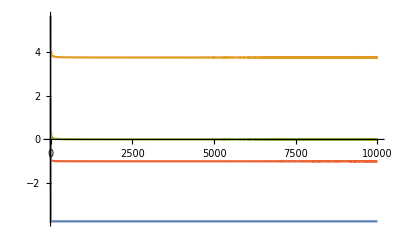

```mathematica
Plot[{(t^3*dtVirtualLeftUVLU[t kx,t ky,t kz,lx,ly,lz,1,0,0,1,1,0,0,-1]/.{kx->1,ky->2,kz->1.2,lx->0.43,ly->0.291,lz->1.34}),(t^3*dtVirtualLeftLU[t kx,t ky,t kz,lx,ly,lz,1,0,0,1,1,0,0,-1]/.{kx->1,ky->2,kz->1.2,lx->0.43,ly->0.291,lz->1.34}),((t^3*dtVirtualLeftUVLU[t kx,t ky,t kz,lx,ly,lz,1,0,0,1,1,0,0,-1]+(t^3*dtVirtualLeftLU[t kx,t ky,t kz,lx,ly,lz,1,0,0,1,1,0,0,-1]))/.{kx->1,ky->2,kz->1.2,lx->0.43,ly->0.291,lz->1.34}),((t^3*dtVirtualLeftUVLU[t kx,t ky,t kz,lx,ly,lz,1,0,0,1,1,0,0,-1]/(t^3*dtVirtualLeftLU[t kx,t ky,t kz,lx,ly,lz,1,0,0,1,1,0,0,-1]))/.{kx->1,ky->2,kz->1.2,lx->0.43,ly->0.291,lz->1.34})},{t,0,10000}]
```

#### Virtual Right UV

```mathematica
dtVirtualRightUVLU[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=((dtNumeratorRightUV[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2k0 2 (k0-p10-p20)]))/.{k0->norm[{0,kx,ky,kz}],MUV->1})
```

#### Test Virtual Right UV

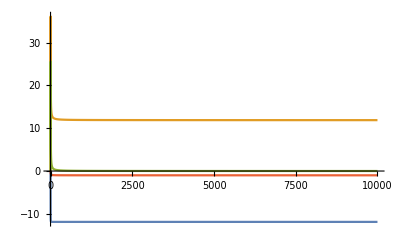

```mathematica
Plot[{(t^3*dtVirtualRightUVLU[kx,ky,kz,t lx,t ly,t lz,1,0,0,1,1,0,0,-1]/.{kx->1,ky->2,kz->1.2,lx->0.43,ly->0.291,lz->1.34}),(t^3*dtVirtualRightLU[kx,ky,kz,t lx,t ly,t lz,1,0,0,1,1,0,0,-1]/.{kx->1,ky->2,kz->1.2,lx->0.43,ly->0.291,lz->1.34}),((t^3*dtVirtualRightUVLU[kx,ky,kz,t lx,t ly,t lz,1,0,0,1,1,0,0,-1]+(t^3*dtVirtualRightLU[kx,ky,kz,t lx,t ly,t lz,1,0,0,1,1,0,0,-1]))/.{kx->1,ky->2,kz->1.2,lx->0.43,ly->0.291,lz->1.34}),((t^3*dtVirtualRightUVLU[kx,ky,kz,t lx,t ly,t lz,1,0,0,1,1,0,0,-1]/(t^3*dtVirtualRightLU[kx,ky,kz,t lx,t ly,t lz,1,0,0,1,1,0,0,-1]))/.{kx->1,ky->2,kz->1.2,lx->0.43,ly->0.291,lz->1.34})},{t,0,10000}]
```

### Real contributions

#### Real right

-Graphics-

Toy model version (on - shell energy delta solved using q0)

```mathematica
dtRealLeft[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=(dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2k0 2(l0-k0)2(l0-p10-p20)]SP[{k0,kx,ky,kz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z},{k0,kx,ky,kz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z}]SP[{l0,lx,ly,lz},{l0,lx,ly,lz}]))/.{p20->-p10+norm[{0,lx,ly,lz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]+l0}/.{l0->k0+norm[{0,lx-kx,ly-kx,lz-kz}]}/.{k0->norm[{0,kx,ky,kz}]}
```

LU version (on - shell energy delta not yet solved)

```mathematica
dtRealLeftLU[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=(dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2k0 2(l0-k0)2(l0-p10-p20)]SP[{k0,kx,ky,kz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z},{k0,kx,ky,kz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z}]SP[{l0,lx,ly,lz},{l0,lx,ly,lz}]))/.{l0 ->p20+p10-norm[{0,lx,ly,lz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]}/.{k0->norm[{0,kx,ky,kz}]}
```

#### Real left

-Graphics-

Toy model version (on - shell energy delta solved using q0)

```mathematica
dtRealRight[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=(dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2l0 2(-l0+k0)2(k0-p10-p20)]SP[{l0,lx,ly,lz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z},{l0,lx,ly,lz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z}]SP[{k0,kx,ky,kz},{k0,kx,ky,kz}]))/.{p20->-p10+norm[{0,kx,ky,kz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]+k0}/.{k0->l0+norm[{0,lx-kx,ly-kx,lz-kz}]}/.{l0->norm[{0,lx,ly,lz}]}
```

LU version (on - shell energy delta not yet solved)

```mathematica
dtRealRightLU[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=(dtNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2l0 2(-l0+k0)2(k0-p10-p20)]SP[{l0,lx,ly,lz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z},{l0,lx,ly,lz}-{p10,p1x,p1y,p1z}-{p20,p2x,p2y,p2z}]SP[{k0,kx,ky,kz},{k0,kx,ky,kz}]))/.{k0 ->p20+p10-norm[{0,kx,ky,kz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]}/.{l0->norm[{0,lx,ly,lz}]}
```

### Cross - section per supergraph

#### Toy model

```mathematica
dtSum[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=dtVirtualLeft[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p2x,p2y,p2z]+dtVirtualRight[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p2x,p2y,p2z]+dtRealLeft[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p2x,p2y,p2z]+dtRealRight[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p2x,p2y,p2z]
```

```mathematica
dtSum[1,2.3,3,4,3,5,6,7,8,9,1,2,6]
```

-54.8683

#### LU

```mathematica
dtLUrep[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_,sigma_,DEBUG_,UV_]:=Module[{vLt,vRt,rLt,rRt,sum,c,uvCT=0},
vLt=vLsol[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z];
vRt=vRsol[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z];
rLt=rLsol[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z];
rRt=rRsol[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z];

c=const[p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]/(Sqrt[Pi]sigma );

If[UV,
uvCT=(vLt^6(Exp[-vLt^2/sigma^2])/(vLdiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])dtVirtualLeftUVLU[vLt*kx,vLt*ky,vLt*kz,vLt*lx,vLt*ly,vLt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z] +vRt^6(Exp[-vRt^2/sigma^2])/(vRdiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])dtVirtualRightUVLU[vRt*kx,vRt*ky,vRt*kz,vRt*lx,vRt*ly,vRt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])];


sum=( vLt^6(Exp[-vLt^2/sigma^2])/(vLdiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])dtVirtualLeftLU[vLt*kx,vLt*ky,vLt*kz,vLt*lx,vLt*ly,vLt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]+vRt^6(Exp[-vRt^2/sigma^2])/(vRdiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])dtVirtualRightLU[vRt*kx,vRt*ky,vRt*kz,vRt*lx,vRt*ly,vRt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]+
rLt^6(Exp[-rLt^2/sigma^2])/(rLdiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])dtRealLeftLU[rLt*kx,rLt*ky,rLt*kz,rLt*lx,rLt*ly,rLt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]+rRt^6(Exp[-rRt^2/sigma^2])/(rRdiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])dtRealRightLU[rRt*kx,rRt*ky,rRt*kz,rRt*lx,rRt*ly,rRt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]);

If[DEBUG,
Print["virtual Left: "];Print[c vLt^6(Exp[-vLt^2/sigma^2])/(vLdiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])dtVirtualLeftLU[vLt*kx,vLt*ky,vLt*kz,vLt*lx,vLt*ly,vLt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]];
Print["virtual Right: "];Print[c vRt^6(Exp[-vRt^2/sigma^2])/(vRdiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])dtVirtualRightLU[vRt*kx,vRt*ky,vRt*kz,vRt*lx,vRt*ly,vRt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]];
Print["real Left: "];Print[c rLt^6(Exp[-rLt^2/sigma^2])/(rLdiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])dtRealLeftLU[rLt*kx,rLt*ky,rLt*kz,rLt*lx,rLt*ly,rLt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]];
Print["real Right: "];Print[c rRt^6(Exp[-rRt^2/sigma^2])/(rRdiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])dtRealRightLU[rRt*kx,rRt*ky,rRt*kz,rRt*lx,rRt*ly,rRt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]];];

c*(sum+uvCT)
];
```

```mathematica
dtLUrep[-0.02018173, 0.062112999,0.0898907771,-0.53934466291,-0.3918568348,0,1,0,0,1,1,0,0,-1,2,True,False]
```

virtual Left:

0.-37.8308 ⅈ

virtual Right:

0.+6.87465×10^-6 ⅈ

real Left:

0.+15.558 ⅈ

real Right:

0.+15.558 ⅈ

0.-6.71471 ⅈ

### Tests of LU expression

#### LU expression test

```mathematica
dtLUrep[-0.02018173, 0.062112999,0.0898907771,-0.53934466291,-0.3918568348,0,1,0,0,1,1,0,0,-1,2,True,False]
Print["-----------"]
Print["virtual Left benchmark: "];
Print["-37.86988"];
Print["virtual Right benchmark: "];
Print["0.00000687466"];
Print["real Left benchmark: "];
Print["15.5581"];
Print["real Right benchmark: "];Print["15.5581"];
```

virtual Left:

0.-37.8308 ⅈ

virtual Right:

0.+6.87465×10^-6 ⅈ

real Left:

0.+15.558 ⅈ

real Right:

0.+15.558 ⅈ

0.-6.71471 ⅈ

-----------

virtual Left benchmark:

-37.86988

virtual Right benchmark:

0.00000687466

real Left benchmark:

15.5581

real Right benchmark:

15.5581

### Tests of Toy model

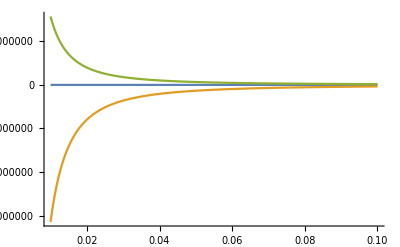

```mathematica
Plot[{dtSum[1,1,1,0.5,0.5,0.5+eps,1,0,0,1,0,0,-1], dtVirtualRight[1,1,1,0.5,0.5,0.5+eps,1,0,0,1,0,0,-1], dtRealRight[1,1,1,0.5,0.5,0.5+eps,1,0,0,1,0,0,-1]},{eps,0.01,0.1},PlotRange->All]
```

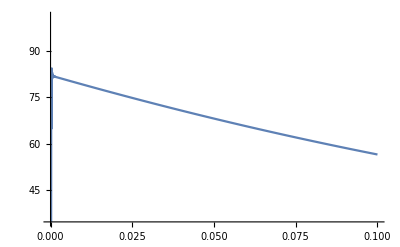

```mathematica
Plot[{dtSum[0.3,0.3,0.3,0.5,0.5,0.5+eps,1,0,0,1,0,0,-1]},{eps,0.0,0.1}]
```

## -Graphics-

### Normalisation

```mathematica
const[p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=0.389379*10^(9)*(gs^2 ge^4 Qd^2 Qe^2(-2 Pi I)^3/(4(2 Pi)^8  SP[{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z},{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]^3))/.{ge->N[Sqrt[4π 1/(132.507`16)]], gs->N[Sqrt[4π 0.118`16]],Qe->1,Qd->1/3}
```

### Causal flow

#### Flow solutions

```mathematica
usualtTch[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=-(p10+p20)/(norm[{0,kx,ky,kz}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}]+norm[{0,kx,ky,kz}+{0,lx,ly,lz}]-norm[{0,lx,ly,lz}])

weirdtTch[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=-(p10+p20)/(norm[{0,kx,ky,kz}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}]+norm[{0,kx,ky,kz}])
```

#### Dirac delta jacobians

```mathematica
usualDiracJTch[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=Dot[Grad[-norm[{0,ax,ay,az}]+norm[{0,sx,sy,sz}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}]+norm[{0,sx,sy,sz}+{0,ax,ay,az}],{sx,sy,sz,ax,ay,az}],{sx,sy,sz,ax,ay,az}]/.{sx->kx,sy->ky,sz->kz,ax->lx,ay->ly,az->lz};

weirdDiracJTch[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=(Dot[Grad[norm[{0,sx,sy,sz}]+norm[{0,sx,sy,sz}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}],{sx,sy,sz}] ,{sx,sy,sz}])/.{sx->kx,sy->ky,sz->kz,ax->lx,ay->ly,az->lz};
```

### Usual Cut

-Graphics-

```mathematica
usualCut[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=((twoNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z},{0,0,0,0}]/(Abs[2 l0 2 (k0+p10+p20) 2(l0+k0)] SP[{k0,kx,ky,kz},{k0,kx,ky,kz}]^2))/.{p20->-p10-k0-norm[{0,kx,ky,kz}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}]}/.{k0->-l0+norm[{0,kx,ky,kz}+{0,lx,ly,lz}]}/.{l0->norm[{0,lx,ly,lz}] })
```

```mathematica
usualCut[kx,ky,kz,lx,ly,lz,1,0,0,1,0,0,-1];
```

```mathematica
usualCutLU[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=((twoNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z},{0,0,0,0}]/(Abs[2 l0 2 (k0+p10+p20) 2(l0+k0)] SP[{k0,kx,ky,kz},{k0,kx,ky,kz}]^2))/.{k0->-l0+norm[{0,kx,ky,kz}+{0,lx,ly,lz}]}/.{l0->norm[{0,lx,ly,lz}] })
```

### Weird Cut 1

This is the true and unique ISR singularity

-Graphics-

```mathematica
weirdCut1[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=-((twoNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z},{0,0,0,0}]/(Abs[2l0 2(k0+p10+p20) 4(k0)^3 ]SP[{k0,kx,ky,kz}+{l0,lx,ly,lz},{k0,kx,ky,kz}+{l0,lx,ly,lz}]))/.{p20->-p10-k0-norm[{0,kx,ky,kz}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}]}/.{l0->norm[{0,lx,ly,lz}]}/.{k0->norm[{0,kx,ky,kz}]})+
((1/Abs[2l0 2(k0+p10+p20) 4(k0)^2])D[twoNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z},{p0,0,0,0}]/(SP[{k0,kx,ky,kz}+{l0,lx,ly,lz}+{p0,0,0,0},{k0,kx,ky,kz}+{l0,lx,ly,lz}+{p0,0,0,0}]),p0])/.{p20->-p10-k0-norm[{0,kx,ky,kz}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}]}/.{l0->norm[{0,lx,ly,lz}]}/.{k0->norm[{0,kx,ky,kz}]}/.{p0->0}
```

```mathematica
weirdCut1LU[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=-((twoNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z},{0,0,0,0}]/(Abs[2l0 2(k0+p10+p20) 4(k0)^3 ]SP[{k0,kx,ky,kz}+{l0,lx,ly,lz},{k0,kx,ky,kz}+{l0,lx,ly,lz}]))/.{l0->norm[{0,lx,ly,lz}]}/.{k0->norm[{0,kx,ky,kz}]})+
((1/Abs[2l0 2(k0+p10+p20) 4(k0)^2])D[twoNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z},{p0,0,0,0}]/(SP[{k0,kx,ky,kz}+{l0,lx,ly,lz}+{p0,0,0,0},{k0,kx,ky,kz}+{l0,lx,ly,lz}+{p0,0,0,0}]),p0])/.{l0->norm[{0,lx,ly,lz}]}/.{k0->norm[{0,kx,ky,kz}]}/.{p0->0}
```

### Weird Cut 2

This one is a diagram without support, and should not be included ultimately.Indeed, there is no such singularity in the original diagram (once energy conservation is applied)

-Graphics-

```mathematica
weirdCut2[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=((twoNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z},{0,0,0,0}]/(Abs[2(k0+l0) 2(k0+p10+p20) 4(k0)^3 ]SP[{l0,lx,ly,lz},{l0,lx,ly,lz}]))/.{p20->-p10-k0-norm[{0,kx,ky,kz}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}]}/.{l0->-k0+norm[{0,lx,ly,lz}+{0,kx,ky,kz}]}/.{k0->-norm[{0,kx,ky,kz}]})-
(((1/Abs[2norm[{0,kx,ky,kz}+{0,lx,ly,lz}] 2(k0+p10+p20) 4(k0)^2])D[twoNumerator[{k0,kx,ky,kz},{-k0-p0+norm[{0,lx,ly,lz}+{0,kx,ky,kz}],lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z},{p0,0,0,0}]/(SP[{-k0-p0+norm[{0,lx,ly,lz}+{0,kx,ky,kz}],lx,ly,lz},{-k0-p0+norm[{0,lx,ly,lz}+{0,kx,ky,kz}],lx,ly,lz}]),p0])/.{p20->-p10-k0-norm[{0,kx,ky,kz}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}]}/.{k0->-norm[{0,kx,ky,kz}]}/.{p0->0})
```

#### Numerator cancellation

It seems that, even without considering the fact that the singularity has no support, it wouldn' t be there to begin with, because the numerator exactly vanishes at the location of the singularity

```mathematica
testf[x_,y_]:=Simplify[(twoNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z},{0,0,0,0}]/.{p20->-p10-k0-norm[{0,kx,ky,kz}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}]}/.{l0->-k0+norm[{0,lx,ly,lz}+{0,kx,ky,kz}]}/.{k0->-norm[{0,kx,ky,kz}]})/.{p10->1,p1x->0,p1y->0,p1z->1,p2x->0,p2y->0,p2z->-1,kx->0,ky->0,kz->-x,lx->0,ly->0,lz->y}]
```

```mathematica
testf[0.3,1]
```

0.

### Cross section per supergraph

#### Toy model

```mathematica
twoSum[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=usualCut[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p2x,p2y,p2z]+weirdCut1[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p2x,p2y,p2z]+weirdCut2[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p2x,p2y,p2z]
```

#### LU

```mathematica
tChLU[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_,sigma_,DEBUG_]:=Module[{vt,rt,sum,c},
vt=usualtTch[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z];
rt=weirdtTch[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z];
(*Print[vt];*)
c=I*const[p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]/(Sqrt[Pi]sigma );

sum=( vt^6(Exp[-vt^2/sigma^2])/(usualDiracJTch[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])usualCutLU[vt*kx,vt*ky,vt*kz,vt*lx,vt*ly,vt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]+rt^6(Exp[-rt^2/sigma^2])/(weirdDiracJTch[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])weirdCut1LU[rt*kx,rt*ky,rt*kz,rt*lx,rt*ly,rt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]);
(*
If[DEBUG,
Print["virtual: "];Print[vt^6(Exp[-vt^2/sigma^2])/(usualTchDiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])usualCutLU[vt*kx,vt*ky,vt*kz,vt*lx,vt*ly,vt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]];
Print["real: "];Print[rt^6(Exp[-rt^2/sigma^2])/(weirdTchDiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])weirdCut1LU[rt*kx,rt*ky,rt*kz,rt*lx,rt*ly,rt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]];
];*)

c*sum
];
```

```mathematica
weirdtChLU[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_,sigma_,DEBUG_]:=Module[{rt,sum,c},
rt=weirdtTch[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z];
(*Print[vt];*)
c=I*const[p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]/(Sqrt[Pi]sigma );

sum=rt^6(Exp[-rt^2/sigma^2])/(weirdDiracJTch[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])weirdCut1LU[rt*kx,rt*ky,rt*kz,rt*lx,rt*ly,rt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z];
(*
If[DEBUG,
Print["virtual: "];Print[vt^6(Exp[-vt^2/sigma^2])/(usualTchDiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])usualCutLU[vt*kx,vt*ky,vt*kz,vt*lx,vt*ly,vt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]];
Print["real: "];Print[rt^6(Exp[-rt^2/sigma^2])/(weirdTchDiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])weirdCut1LU[rt*kx,rt*ky,rt*kz,rt*lx,rt*ly,rt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]];
];*)

c*sum
];
```

```mathematica
usualtChLU[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_,sigma_,DEBUG_]:=Module[{vt,sum,c},
vt=usualtTch[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z];
(*Print[vt];*)
c=I*const[p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]/(Sqrt[Pi]sigma );

sum=( vt^6(Exp[-vt^2/sigma^2])/(usualDiracJTch[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])usualCutLU[vt*kx,vt*ky,vt*kz,vt*lx,vt*ly,vt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]);
(*
If[DEBUG,
Print["virtual: "];Print[vt^6(Exp[-vt^2/sigma^2])/(usualTchDiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])usualCutLU[vt*kx,vt*ky,vt*kz,vt*lx,vt*ly,vt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]];
Print["real: "];Print[rt^6(Exp[-rt^2/sigma^2])/(weirdTchDiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])weirdCut1LU[rt*kx,rt*ky,rt*kz,rt*lx,rt*ly,rt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]];
];*)

c*sum
];
```

```mathematica
tChLU[0,0.2,0.5,0,0,1,1,0,0,1,1,0,0,-1,0.2,False]
```

-1.52736×10^-34+0. ⅈ

### Tests of LU expression

#### Cancellations for the LU expression

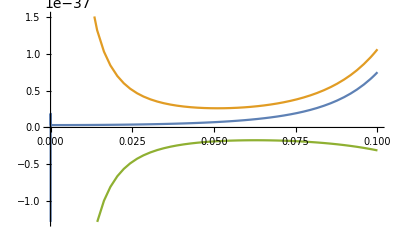

```mathematica
Plot[{tChLU[0,eps,0.5,0,0,1,-1,0,0,1,-1,0,0,-1,0.2,False],weirdtChLU[0,eps,0.5,0,0,1,-1,0,0,1,-1,0,0,-1,0.2,False],usualtChLU[0,eps,0.5,0,0,1,-1,0,0,1,-1,0,0,-1,0.2,False]},{eps,0,0.1}]
```

General::munfl: Exp[-1.01285×10^16] is too small to represent as a normalized machine number; precision may be lost.

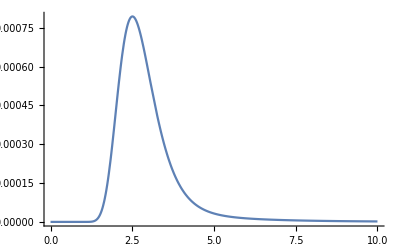

840002.

```mathematica
Plot[tChLU[0,eps,-0.3,0,0,1,-1,0,0,1,-1,0,0,-1,0.2,False],{eps,0,10},PlotRange->All]
usualtTch[0,0.001,-0.3,0,0,1,-1,0,0,1,-1,0,0,-1]
```

#### Integration test for LU expression

```mathematica
Table[NIntegrate[tChLU[kx,ky,kz,lx,ly,lz,1,0,0,1,1,0,0,-1,1,False],{kx,-2,2},{ky,-2,2},{kz,-2,2},{lx,-2,2},{ly,-2,2},{lz,-2,2},Method->"AdaptiveMonteCarlo",PrecisionGoal->5,MaxPoints->1000000,MaxRecursion->1000],{i,1,5}]
```

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 555.15+0. ⅈ and 2.2067 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 552.099+0. ⅈ and 2.31443 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained 554.223+0. ⅈ and 2.35607 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

$Aborted

### Tests of Toy model

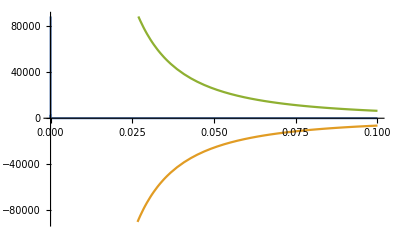

```mathematica
Plot[{weirdCut1[0,eps,0.5,0,0,1,1,0,0,1,0,0,-1]+usualCut[0,eps,0.5,0,0,1,1,0,0,1,0,0,-1],usualCut[0,eps,0.5,0,0,1,1,0,0,1,0,0,-1],weirdCut1[0,eps,0.5,0,0,1,1,0,0,1,0,0,-1]},{eps,0,0.1}]
```

Look at Weird Cut 2 cancellation folder for explanation of the absence of the following singularity

```mathematica
den[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=(1/SP[{-k0-p0+norm[{0,lx,ly,lz}+{0,kx,ky,kz}],lx,ly,lz},{-k0-p0+norm[{0,lx,ly,lz}+{0,kx,ky,kz}],lx,ly,lz}])/.{p20->-p10-k0-norm[{0,kx,ky,kz}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}]}/.{k0->-norm[{0,kx,ky,kz}]}/.{p0->0}
```

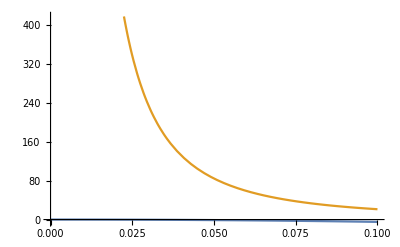

```mathematica
Plot[{weirdCut2[0,eps,-0.3,0,0,1,1,0,0,1,0,0,-1]+usualCut[0,eps,-0.3,0,0,1,1,0,0,1,0,0,-1],den[0,eps,-0.3,0,0,1,1,0,0,1,0,0,-1]},{eps,0,0.1}]
```

## -Graphics-

### Normalisation

```mathematica
const[p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=0.389379*10^(9)*(gs^2 ge^4 Qd^2 Qe^2(-2 Pi I)^3/(4(2 Pi)^8  SP[{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z},{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]^3))/.{ge->N[Sqrt[4π 1/(132.507`16)]], gs->N[Sqrt[4π 0.118`16]],Qe->1,Qd->1/3}
```

### Causal flow

#### Flow solutions

```mathematica
usualtUch[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=-(p10+p20)/(norm[{0,kx,ky,kz}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}]+norm[{0,kx,ky,kz}+{0,lx,ly,lz}]-norm[{0,lx,ly,lz}])

weirdtUch1[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=-(p10+p20)/(norm[{0,kx,ky,kz}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}]+norm[{0,kx,ky,kz}])

weirdtUch2[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=-(p10+p20)/(norm[{0,kx,ky,kz}+{0,lx,ly,lz}]+norm[{0,kx,ky,kz}+{0,lx,ly,lz}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}])

newtUch1[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=-(p10+p20)/(norm[{0,kx,ky,kz}+{0,lx,ly,lz}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}]+norm[{0,lx,ly,lz}]+norm[{0,kx,ky,kz}])

newtUch2[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=-(p10+p20)/(norm[{0,kx,ky,kz}+{0,lx,ly,lz}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}]+norm[{0,kx,ky,kz}+{0,lx,ly,lz}])

newtUch3[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=-(p10+p20)/(norm[{0,kx,ky,kz}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}]+norm[{0,kx,ky,kz}])
```

#### Dirac delta jacobians

```mathematica
usualDiracJUch[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=Dot[Grad[-norm[{0,ax,ay,az}]+norm[{0,sx,sy,sz}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}]+norm[{0,sx,sy,sz}+{0,ax,ay,az}],{sx,sy,sz,ax,ay,az}],{sx,sy,sz,ax,ay,az}]/.{sx->kx,sy->ky,sz->kz,ax->lx,ay->ly,az->lz};

weirdDiracJUch1[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=(Dot[Grad[norm[{0,sx,sy,sz}]+norm[{0,sx,sy,sz}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}],{sx,sy,sz}] ,{sx,sy,sz}])/.{sx->kx,sy->ky,sz->kz,ax->lx,ay->ly,az->lz};

weirdDiracJUch2[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=(Dot[Grad[norm[{0,sx,sy,sz}+{0,ax,ay,az}]+norm[{0,sx,sy,sz}+{0,ax,ay,az}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}],{sx,sy,sz,ax,ay,az}] ,{sx,sy,sz,ax,ay,az}])/.{sx->kx,sy->ky,sz->kz,ax->lx,ay->ly,az->lz};

newDiracJUch1[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=(Dot[Grad[norm[{0,ax,ay,az}]+norm[{0,sx,sy,sz}+{0,ax,ay,az}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}]+norm[{0,sx,sy,sz}],{sx,sy,sz,ax,ay,az}] ,{sx,sy,sz,ax,ay,az}])/.{sx->kx,sy->ky,sz->kz,ax->lx,ay->ly,az->lz};

newDiracJUch2[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=(Dot[Grad[norm[{0,sx,sy,sz}+{0,ax,ay,az}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}]+norm[{0,sx,sy,sz}+{0,ax,ay,az}],{sx,sy,sz,ax,ay,az}] ,{sx,sy,sz,ax,ay,az}])/.{sx->kx,sy->ky,sz->kz,ax->lx,ay->ly,az->lz};

newDiracJUch3[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=(Dot[Grad[norm[{0,sx,sy,sz}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}]+norm[{0,sx,sy,sz}],{sx,sy,sz,ax,ay,az}] ,{sx,sy,sz,ax,ay,az}])/.{sx->kx,sy->ky,sz->kz,ax->lx,ay->ly,az->lz};
```

### Usual cut

-Graphics-

```mathematica
uChannelUsualCut[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=((uChannelNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2 l0 2 (k0+l0)2(k0+p10+p20)]SP[{k0,kx,ky,kz},{k0,kx,ky,kz}]SP[{k0,kx,ky,kz}+{l0,lx,ly,lz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z},{k0,kx,ky,kz}+{l0,lx,ly,lz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]))/.{p20->-p10-k0-norm[{0,kx,ky,kz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]}/.{k0->-l0+norm[{0,kx,ky,kz}+{0,lx,ly,lz}]}/.{l0->norm[{0,lx,ly,lz}]})

uChannelUsualCut[kx,ky,kz,lx,ly,lz,qx,qy,qz,1,1];
```

```mathematica
uChannelUsualCutLU[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=((uChannelNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2 l0 2 (k0+l0)2(k0+p10+p20)]SP[{k0,kx,ky,kz},{k0,kx,ky,kz}]SP[{k0,kx,ky,kz}+{l0,lx,ly,lz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z},{k0,kx,ky,kz}+{l0,lx,ly,lz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]))/.{k0->-l0+norm[{0,kx,ky,kz}+{0,lx,ly,lz}]}/.{l0->norm[{0,lx,ly,lz}]})
```

### Weird cut 1

-Graphics-

```mathematica
uChannelWeirdCut1[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=((uChannelNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2l0 2k0 2(k0+p10+p20)]SP[{k0,kx,ky,kz}+{l0,lx,ly,lz},{k0,kx,ky,kz}+{l0,lx,ly,lz}]SP[{k0,kx,ky,kz}+{l0,lx,ly,lz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z},{k0,kx,ky,kz}+{l0,lx,ly,lz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]))/.{p20->-p10-k0-norm[{0,kx,ky,kz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]}/.{k0->norm[{0,kx,ky,kz}]}/.{l0->norm[{0,lx,ly,lz}]})

uChannelWeirdCut1[kx,ky,kz,lx,ly,lz,qx,qy,qz,1,1];
```

```mathematica
uChannelWeirdCut1LU[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=((uChannelNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2l0 2k0 2(k0+p10+p20)]SP[{k0,kx,ky,kz}+{l0,lx,ly,lz},{k0,kx,ky,kz}+{l0,lx,ly,lz}]SP[{k0,kx,ky,kz}+{l0,lx,ly,lz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z},{k0,kx,ky,kz}+{l0,lx,ly,lz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]))/.{k0->norm[{0,kx,ky,kz}]}/.{l0->norm[{0,lx,ly,lz}]})
```

### Weird Cut 2

-Graphics-

```mathematica
uChannelWeirdCut2[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=((uChannelNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2 l0 2 (k0+l0)2(k0+l0+p10+p20)]SP[{k0,kx,ky,kz},{k0,kx,ky,kz}]SP[{k0,kx,ky,kz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z},{k0,kx,ky,kz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]))/.{p20->-p10-l0-k0-norm[{0,kx,ky,kz}+{0,lx,ly,lz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]}/.{k0->-l0+norm[{0,kx,ky,kz}+{0,lx,ly,lz}]}/.{l0->norm[{0,lx,ly,lz}]})

uChannelWeirdCut2[0,0.0001,0.5,0,0,-0.3,1,0,0,1,0,0,-1]
```

2.37037×10^9

```mathematica
uChannelWeirdCut2LU[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=((uChannelNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2 l0 2 (k0+l0)2(k0+l0+p10+p20)]SP[{k0,kx,ky,kz},{k0,kx,ky,kz}]SP[{k0,kx,ky,kz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z},{k0,kx,ky,kz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]))/.{k0->-l0+norm[{0,kx,ky,kz}+{0,lx,ly,lz}]}/.{l0->norm[{0,lx,ly,lz}]})
```

### New Cut 1

-Graphics-

```mathematica
uChannelNewCut1[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=((uChannelNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2 k0 2 (l0)2(k0+l0+p10+p20)]SP[{k0,kx,ky,kz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z},{k0,kx,ky,kz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]SP[{k0,kx,ky,kz}+{l0,lx,ly,lz},{k0,kx,ky,kz}+{l0,lx,ly,lz}]))/.{p20->-p10-k0-l0-norm[{0,kx,ky,kz}+{0,lx,ly,lz}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}]}/.{l0->norm[{0,lx,ly,lz}]}/.{k0->norm[{0,kx,ky,kz}]})
```

```mathematica
uChannelNewCut1LU[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=((uChannelNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2 k0 2 (l0)2(k0+l0+p10+p20)]SP[{k0,kx,ky,kz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z},{k0,kx,ky,kz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]SP[{k0,kx,ky,kz}+{l0,lx,ly,lz},{k0,kx,ky,kz}+{l0,lx,ly,lz}]))/.{l0->norm[{0,lx,ly,lz}]}/.{k0->norm[{0,kx,ky,kz}]})
```

### New Cut 2

-Graphics-

```mathematica
uChannelNewCut2[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=((uChannelNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2 k0 2 (l0+k0)2(k0+l0+p10+p20)]SP[{k0,kx,ky,kz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z},{k0,kx,ky,kz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]SP[{l0,lx,ly,lz},{l0,lx,ly,lz}]))/.{p20->-p10-k0-l0-norm[{0,kx,ky,kz}+{0,lx,ly,lz}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}]}/.{l0->-k0+norm[{0,lx,ly,lz}+{0,kx,ky,kz}]}/.{k0->-norm[{0,kx,ky,kz}]})
```

```mathematica
uChannelNewCut2LU[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=((uChannelNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2 k0 2 (l0+k0)2(k0+l0+p10+p20)]SP[{k0,kx,ky,kz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z},{k0,kx,ky,kz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]SP[{l0,lx,ly,lz},{l0,lx,ly,lz}]))/.{l0->-k0+norm[{0,lx,ly,lz}+{0,kx,ky,kz}]}/.{k0->-norm[{0,kx,ky,kz}]})
```

### New Cut 3

-Graphics-

```mathematica
uChannelNewCut3[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=((uChannelNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2 k0 2 (k0+p10+p20)2(k0+l0+p10+p20)]SP[{k0,kx,ky,kz}+{l0,lx,ly,lz},{k0,kx,ky,kz}+{l0,lx,ly,lz}]SP[{l0,lx,ly,lz},{l0,lx,ly,lz}]))/.{l0->-k0-p10-p20+norm[{0,lx,ly,lz}+{0,kx,ky,kz}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}]}/.{p20->-p10-k0-norm[{0,kx,ky,kz}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}]}/.{k0->norm[{0,kx,ky,kz}]})
```

```mathematica
uChannelNewCut3LU[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=(*((((*SP[{k0,kx,ky,kz}+{l0,lx,ly,lz},{k0,kx,ky,kz}+{l0,lx,ly,lz}]*)SP[{l0,lx,ly,lz},{l0,lx,ly,lz}]))/.{l0->-k0-p10-p20+norm[{0,lx,ly,lz}+{0,kx,ky,kz}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}]}/.{k0->norm[{0,kx,ky,kz}]})*)((uChannelNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2 k0 2 (k0+p10+p20)2(k0+l0+p10+p20)]SP[{k0,kx,ky,kz}+{l0,lx,ly,lz},{k0,kx,ky,kz}+{l0,lx,ly,lz}]SP[{l0,lx,ly,lz},{l0,lx,ly,lz}]))/.{l0->-k0-p10-p20+norm[{0,lx,ly,lz}+{0,kx,ky,kz}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}]}/.(*{k0->-p20-p10-norm[{0,kx,ky,kz}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}]})/.*){k0->norm[{0,kx,ky,kz}]})
```

### Cross section per supergraph

#### Toy model

```mathematica
uChannelSum[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=uChannelUsualCut[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p2x,p2y,p2z]+uChannelWeirdCut1[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p2x,p2y,p2z]+uChannelWeirdCut2[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p2x,p2y,p2z]
```

#### LU

```mathematica
uChannelSumLU[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_,sigma_,DEBUG_]:=Module[{vt,rt1,rt2,nt1,nt2,nt3,sum,c},
vt=usualtUch[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z];
rt1=weirdtUch1[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z];
rt2=weirdtUch2[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z];
nt1=newtUch1[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z];
nt2=newtUch2[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z];
nt3=newtUch3[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z];
(*Print[vt];
Print[rt1];
Print[rt2];*)
c=I*const[p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]/(Sqrt[Pi]sigma );

sum=(vt^6(Exp[-vt^2/sigma^2])/(usualDiracJUch[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])uChannelUsualCutLU[vt*kx,vt*ky,vt*kz,vt*lx,vt*ly,vt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]+rt1^6(Exp[-rt1^2/sigma^2])/(weirdDiracJUch1[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])uChannelWeirdCut1LU[rt1*kx,rt1*ky,rt1*kz,rt1*lx,rt1*ly,rt1*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]+rt2^6(Exp[-rt2^2/sigma^2])/(weirdDiracJUch2[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])uChannelWeirdCut2LU[rt2*kx,rt2*ky,rt2*kz,rt2*lx,rt2*ly,rt2*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]+nt1^6(Exp[-nt1^2/sigma^2])/(newDiracJUch1[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])uChannelNewCut1LU[nt1*kx,nt1*ky,nt1*kz,nt1*lx,nt1*ly,nt1*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]+nt2^6(Exp[-nt2^2/sigma^2])/(newDiracJUch2[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])uChannelNewCut2LU[nt2*kx,nt2*ky,nt2*kz,nt2*lx,nt2*ly,nt2*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]+nt3^6(Exp[-nt3^2/sigma^2])/(newDiracJUch3[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])uChannelNewCut3LU[nt3*kx,nt3*ky,nt3*kz,nt3*lx,nt3*ly,nt3*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]
);

If[DEBUG,
Print["usual: "];Print[vt^6(Exp[-vt^2/sigma^2])/(usualDiracJUch[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])uChannelUsualCutLU[vt*kx,vt*ky,vt*kz,vt*lx,vt*ly,vt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]];
Print["usual no measure:"];
Print[uChannelUsualCutLU[vt*kx,vt*ky,vt*kz,vt*lx,vt*ly,vt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]];
Print["measure:"];
Print[vt^6(Exp[-vt^2/sigma^2])/(usualDiracJUch[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])];
Print[usualDiracJUch[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]];
Print[vt];
Print[(Exp[-vt^2/sigma^2])];
Print["weird1: "];Print[rt1^6(Exp[-rt1^2/sigma^2])/(weirdDiracJUch1[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])uChannelWeirdCut1LU[rt1*kx,rt1*ky,rt1*kz,rt1*lx,rt1*ly,rt1*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]];
Print["weird2: "];Print[rt2^6(Exp[-rt2^2/sigma^2])/(weirdDiracJUch2[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])uChannelWeirdCut2LU[rt2*kx,rt2*ky,rt2*kz,rt2*lx,rt2*ly,rt2*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]];
];

c*sum
];
```

```mathematica
uChannelSumLU[1,2,3.2,4,5,6,1,0,0,1,1,0,0,-1,1,False]
```

2.34463×10^-6+0. ⅈ

#### LU single integrands

```mathematica
usualUChannelSumLU[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_,sigma_,DEBUG_]:=Module[{vt,sum,c},
vt=usualtUch[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z];
c=I*const[p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]/(Sqrt[Pi]sigma );
sum=( vt^6(Exp[-vt^2/sigma^2])/(usualDiracJUch[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])uChannelUsualCutLU[vt*kx,vt*ky,vt*kz,vt*lx,vt*ly,vt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]);

c*sum
];

weird1UChannelSumLU[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_,sigma_,DEBUG_]:=Module[{rt1,sum,c},
rt1=weirdtUch1[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z];
c=I*const[p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]/(Sqrt[Pi]sigma );
sum=( rt1^6(Exp[-rt1^2/sigma^2])/(weirdDiracJUch1[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])uChannelWeirdCut1LU[rt1*kx,rt1*ky,rt1*kz,rt1*lx,rt1*ly,rt1*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]);

c*sum
];

weird2UChannelSumLU[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_,sigma_,DEBUG_]:=Module[{rt2,sum,c},
rt2=weirdtUch2[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z];
c=I*const[p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]/(Sqrt[Pi]sigma );
sum=(rt2^6(Exp[-rt2^2/sigma^2])/(weirdDiracJUch2[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])uChannelWeirdCut2LU[rt2*kx,rt2*ky,rt2*kz,rt2*lx,rt2*ly,rt2*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]);

c*sum
];

newUChannelSumLU1[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_,sigma_,DEBUG_]:=Module[{nt,sum,c},
nt=newtUch1[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z];
c=I*const[p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]/(Sqrt[Pi]sigma );
sum=(nt^6(Exp[-nt^2/sigma^2])/(newDiracJUch1[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])uChannelNewCut1LU[nt*kx,nt*ky,nt*kz,nt*lx,nt*ly,nt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]);

c*sum
];

newUChannelSumLU2[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_,sigma_,DEBUG_]:=Module[{nt,sum,c},
nt=newtUch2[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z];
c=I*const[p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]/(Sqrt[Pi]sigma );
sum=(nt^6(Exp[-nt^2/sigma^2])/(newDiracJUch2[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])uChannelNewCut2LU[nt*kx,nt*ky,nt*kz,nt*lx,nt*ly,nt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]);

c*sum
];

newUChannelSumLU3[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_,sigma_,DEBUG_]:=Module[{nt,sum,c},
nt=newtUch3[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z];
c=I*const[p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]/(Sqrt[Pi]sigma );
sum=(nt^6(Exp[-nt^2/sigma^2])/(newDiracJUch3[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])uChannelNewCut3LU[nt*kx,nt*ky,nt*kz,nt*lx,nt*ly,nt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]);

c*sum
];
```

```mathematica
uChannelSumLU[0,0.001,0.5,0,0,0.3,-1,0,0,1,-1,0,0,-1,1,False];
```

### Tests of LU expression

#### Cancellations for the LU expression

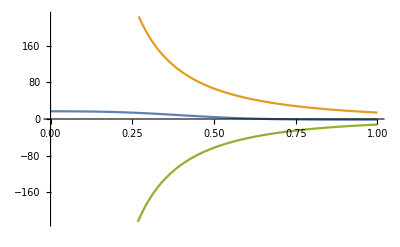

```mathematica
Plot[{uChannelSumLU[0,eps,0.5,0,0,0.3,-1,0,0,1,-1,0,0,-1,1,False],weird2UChannelSumLU[0,eps,0.5,0,0,0.3,-1,0,0,1,-1,0,0,-1,1,False],newUChannelSumLU1[0,eps,0.5,0,0,0.3,-1,0,0,1,-1,0,0,-1,1,False](*,usualUChannelSumLU[0,eps,0.5,0,0,0.3,1,0,0,1,1,0,0,-1,1,False],weird1UChannelSumLU[0,eps,0.5,0,0,0.3,1,0,0,1,1,0,0,-1,1,False]*)(*weird2UChannelSumLU[0,eps,0.5,0,0,0.3,1,0,0,1,1,0,0,-1,1,False],*)(*usualUChannelSumLU[0,eps,0.5,0,0,0.3,1,0,0,1,1,0,0,-1,1,False]+weird1UChannelSumLU[0,eps,0.5,0,0,0.3,1,0,0,1,1,0,0,-1,1,False]*)},{eps,0,1}]
```

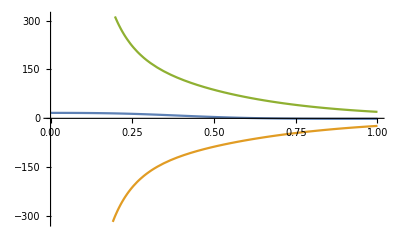

```mathematica
Plot[{uChannelSumLU[0,eps,0.5,0,0,0.3,-1,0,0,1,-1,0,0,-1,1,False],usualUChannelSumLU[0,eps,0.5,0,0,0.3,-1,0,0,1,-1,0,0,-1,1,False],weird1UChannelSumLU[0,eps,0.5,0,0,0.3,-1,0,0,1,-1,0,0,-1,1,False]},{eps,0,1}]
```

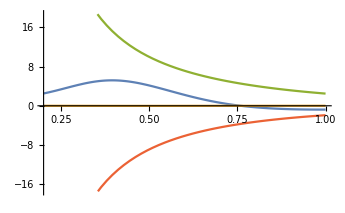

```mathematica
Plot[{uChannelSumLU[0,eps,0.3,0,0,0.5,-1,0,0,1,-1,0,0,-1,1,False],newUChannelSumLU3[0,eps,0.3,0,0,0.5,-1,0,0,1,-1,0,0,-1,1,False],weird2UChannelSumLU[0,eps,0.3,0,0,0.5,-1,0,0,1,-1,0,0,-1,1,False],newUChannelSumLU1[0,eps,0.3,0,0,0.5,-1,0,0,1,-1,0,0,-1,1,False]},{eps,0.2,1}]
```

General::munfl: Exp[-1.32291×10^18] is too small to represent as a normalized machine number; precision may be lost.

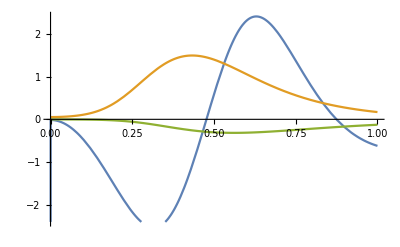

```mathematica
Plot[{uChannelSumLU[0,eps,-0.3,0,0,0.5,-1,0,0,1,-1,0,0,-1,1,False],newUChannelSumLU3[0,eps,-0.3,0,0,0.5,1,0,0,1,1,0,0,-1,1,False],weird1UChannelSumLU[0,eps,-0.3,0,0,0.5,1,0,0,1,1,0,0,-1,1,False]},{eps,0,1}]
```

#### Integration test for LU expression

```mathematica
Table[NIntegrate[uChannelSumLU[kx,ky,kz,lx,ly,lz,-1,0,0,1,-1,0,0,-1,1,False],{kx,-2,2},{ky,-2,2},{kz,-2,2},{lx,-2,2},{ly,-2,2},{lz,-2,2},Method->"AdaptiveMonteCarlo",PrecisionGoal->5,MaxPoints-> 1000000,MaxRecursion->1000],{i,1,5}]
```

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -97.8433+0. ⅈ and 0.268955 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -97.5876+0. ⅈ and 0.275995 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 1000100 integrand evaluations. NIntegrate obtained -98.085+0. ⅈ and 0.266456 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

{-97.8433+0. ⅈ,-97.5876+0. ⅈ,-98.085+0. ⅈ,-98.1762+0. ⅈ,-97.4448+0. ⅈ}

### Tests of Toy model

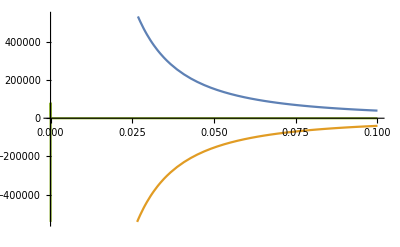

```mathematica
Plot[{uChannelWeirdCut2[0,eps,0.5,0,0,0.3,1,0,0,1,0,0,-1],uChannelNewCut1[0,eps,0.5,0,0,0.3,1,0,0,1,0,0,-1],uChannelWeirdCut2[0,eps,0.5,0,0,0.3,1,0,0,1,0,0,-1]+uChannelNewCut1[0,eps,0.5,0,0,0.3,1,0,0,1,0,0,-1]},{eps,0,0.1}]
```

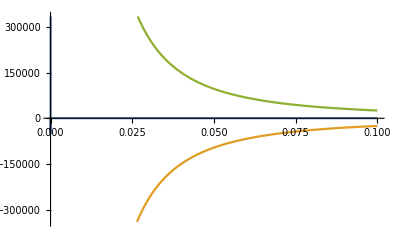

```mathematica
Plot[{uChannelWeirdCut1[0,eps,0.5,0,0,0.3,1,0,0,1,0,0,-1]+uChannelUsualCut[0,eps,0.5,0,0,0.3,1,0,0,1,0,0,-1],uChannelUsualCut[0,eps,0.5,0,0,0.3,1,0,0,1,0,0,-1],uChannelWeirdCut1[0,eps,0.5,0,0,0.3,1,0,0,1,0,0,-1],},{eps,0,0.1}]
```

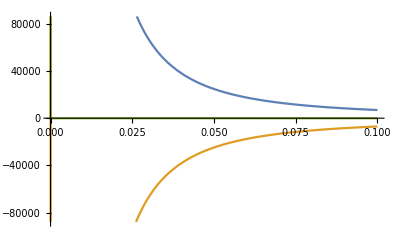

```mathematica
Plot[{uChannelWeirdCut1[0,eps,0.5,0,0,-0.3,1,0,0,1,0,0,-1],uChannelNewCut1[0,eps,0.5,0,0,-0.3,1,0,0,1,0,0,-1], uChannelWeirdCut1[0,eps,0.5,0,0,-0.3,1,0,0,1,0,0,-1]+uChannelNewCut1[0,eps,0.5,0,0,-0.3,1,0,0,1,0,0,-1]},{eps,0,0.1}]
```

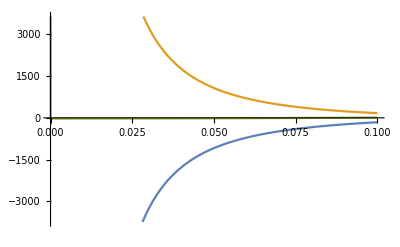

```mathematica
Plot[{uChannelWeirdCut2[0,eps,-0.3,0,0,0.5,1,0,0,1,0,0,-1],uChannelNewCut2[0,eps,-0.3,0,0,0.5,1,0,0,1,0,0,-1], uChannelWeirdCut2[0,eps,-0.3,0,0,0.5,1,0,0,1,0,0,-1]+uChannelNewCut2[0,eps,-0.3,0,0,0.5,1,0,0,1,0,0,-1]},{eps,0,0.1}]
```

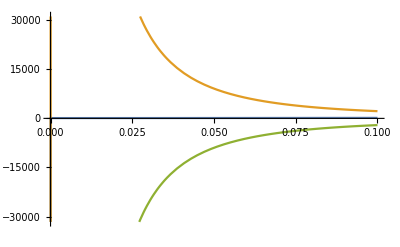

```mathematica
Plot[{uChannelWeirdCut2[0,eps,0.5,0,0,-0.3,1,0,0,1,0,0,-1]+uChannelUsualCut[0,eps,0.5,0,0,-0.3,1,0,0,1,0,0,-1],uChannelWeirdCut2[0,eps,0.5,0,0,-0.3,1,0,0,1,0,0,-1],uChannelUsualCut[0,eps,0.5,0,0,-0.3,1,0,0,1,0,0,-1]},{eps,0,0.1}]
```

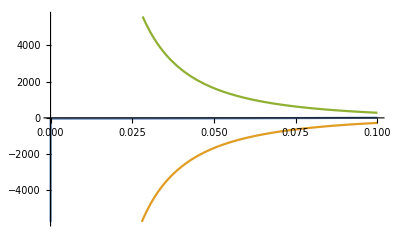

```mathematica
Plot[{uChannelWeirdCut1[0,eps,-0.3,0,0,0.5,1,0,0,1,0,0,-1]+uChannelNewCut3[0,eps,-0.3,0,0,0.5,1,0,0,1,0,0,-1],uChannelWeirdCut1[0,eps,-0.3,0,0,0.5,1,0,0,1,0,0,-1],uChannelNewCut3[0,eps,-0.3,0,0,0.5,1,0,0,1,0,0,-1]},{eps,0,0.1}]
```

## -Graphics-

### Only cut

This diagram has no singularities

```mathematica
sChannelBub[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=((sChannelBubNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2l0 2 (k0+p10+p20-l0)2 k0] SP[{k0,kx,ky,kz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z},{k0,kx,ky,kz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]^2))/.{p20->-p10+l0-k0+norm[{0,kx,ky,kz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}-{0,lx,ly,lz}]}/.{k0->norm[{0,kx,ky,kz}]}/.{l0->norm[{0,lx,ly,lz}]})

sChannelBub[kx,ky,kz,lx,ly,lz,1,0,0,1,0,0,-1];
```

```mathematica
sChannelBubLU[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=((sChannelBubNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2l0 2 (k0+p10+p20-l0)2 k0] SP[{k0,kx,ky,kz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z},{k0,kx,ky,kz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]^2))/.{k0->norm[{0,kx,ky,kz}]}/.{l0->norm[{0,lx,ly,lz}]})
```

```mathematica
sChannelBubLU[1,2,3,4,5,6,1,0,0,1,1,0,0,-1];
```

### Cross section per supergraph

```mathematica
sChannelSum[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=sChannelBub[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p2x,p2y,p2z]
```

## -Graphics-

### Normalisation

```mathematica
const[p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=0.389379*10^(9)*(gs^2 ge^4 Qd^2 Qe^2(-2 Pi I)^3/(4(2 Pi)^8  SP[{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z},{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]^3))/.{ge->N[Sqrt[4π 1/(132.507`16)]], gs->N[Sqrt[4π 0.118`16]],Qe->1,Qd->1/3}
```

### Causal flow

#### Flow Solutions

```mathematica
rSolBub[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=(p10+p20)/(norm[{0,lx,ly,lz}]+norm[{0,kx,ky,kz}-{0,lx,ly,lz}]+norm[{0,kx,ky,kz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]);
vSolBub[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=(p10+p20)/(norm[{0,kx,ky,kz}]+norm[{0,kx,ky,kz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]);
```

#### Dirac Delta Jacobians

```mathematica
rSolBubDiracJ[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=Dot[Grad[norm[{0,ax,ay,az}]+norm[{0,sx,sy,sz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]+norm[{0,sx,sy,sz}-{0,ax,ay,az}],{sx,sy,sz,ax,ay,az}],{sx,sy,sz,ax,ay,az}]/.{sx->kx,sy->ky,sz->kz,ax->lx,ay->ly,az->lz};
vSolBubDiracJ[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=Dot[Grad[norm[{0,sx,sy,sz}]+norm[{0,sx,sy,sz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}],{sx,sy,sz}],{sx,sy,sz}]/.{sx->kx,sy->ky,sz->kz};
```

### Real cut

-Graphics-

Toy model version (on-shell energy delta solved using q0)

```mathematica
bdReal[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=((bubNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z},{0,0,0,0}]/(Abs[2 l0 2 (k0-l0)2(k0-p10-p20)]SP[{k0,kx,ky,kz},{k0,kx,ky,kz}]^2))/.{p20->-p10+k0+norm[{0,kx,ky,kz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]}/.{k0->l0+norm[{0,kx,ky,kz}-{0,lx,ly,lz}]}/.{l0->norm[{0,lx,ly,lz}]})
```

LU version (on - shell energy delta not yet solved)

```mathematica
bdRealLU[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=((bubNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z},{0,0,0,0}]/(Abs[2 l0 2 (k0-l0)2(k0-p10-p20)]SP[{k0,kx,ky,kz},{k0,kx,ky,kz}]^2))/.{k0->p10+p20-norm[{0,kx,ky,kz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]}/.{l0->norm[{0,lx,ly,lz}]})
```

### Virtual cut

-Graphics-

Toy model version (on-shell energy delta solved using q0)

```mathematica
bdVirtual[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=(D[((bubNumerator[{k0,kx,ky,kz},{norm[{0,lx,ly,lz}],lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z},{p0,0,0,0}]/(Abs[(2 k0)^2 2(k0-p10-p20)2norm[{0,lx,ly,lz}]]SP[{k0,kx,ky,kz}+{p0,0,0,0}-{norm[{0,lx,ly,lz}],lx,ly,lz},{k0,kx,ky,kz}+{p0,0,0,0}-{norm[{0,lx,ly,lz}],lx,ly,lz}]))+(bubNumerator[{k0,kx,ky,kz},{p0+k0+norm[{0,lx,ly,lz}-{0,kx,ky,kz}],lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z},{p0,0,0,0}]/(Abs[(2 k0)^2 2(k0-p10-p20)2 norm[{0,lx,ly,lz}-{0,kx,ky,kz}]]SP[{p0+k0+norm[{0,lx,ly,lz}-{0,kx,ky,kz}],lx,ly,lz},{p0+k0+norm[{0,lx,ly,lz}-{0,kx,ky,kz}],lx,ly,lz}]))),p0]/.{p0->0}/.{p20->-p10+k0+norm[{0,kx,ky,kz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]}/.{k0->norm[{0,kx,ky,kz}]})
bdVirtual[kx,ky,kz,lx,ly,lz,1,0,0,1,0,0,-1];
```

LU version (on - shell energy delta not yet solved)

```mathematica
bdVirtualLU[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=(D[((bubNumerator[{k0,kx,ky,kz},{norm[{0,lx,ly,lz}],lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z},{p0,0,0,0}]/(Abs[(2 k0)^2 2(k0-p10-p20)2norm[{0,lx,ly,lz}]]SP[{k0,kx,ky,kz}+{p0,0,0,0}-{norm[{0,lx,ly,lz}],lx,ly,lz},{k0,kx,ky,kz}+{p0,0,0,0}-{norm[{0,lx,ly,lz}],lx,ly,lz}]))+(bubNumerator[{k0,kx,ky,kz},{p0+k0+norm[{0,lx,ly,lz}-{0,kx,ky,kz}],lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z},{p0,0,0,0}]/(Abs[(2 k0)^2 2(k0-p10-p20)2 norm[{0,lx,ly,lz}-{0,kx,ky,kz}]]SP[{p0+k0+norm[{0,lx,ly,lz}-{0,kx,ky,kz}],lx,ly,lz},{p0+k0+norm[{0,lx,ly,lz}-{0,kx,ky,kz}],lx,ly,lz}]))),p0]/.{p0->0}/.{k0->p10+p20-norm[{0,kx,ky,kz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]})
bdVirtualLU[kx,ky,kz,lx,ly,lz,1,0,0,1,1,0,0,-1];
```

### UV counter-term

#### Bubble CT

```mathematica
bd4DCTLTD[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=((1/2)((D[-2(l0-k0) bubNumerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z},{0,0,0,0}]/(Abs[(2k0)^2 2(k0-p10-p20)](l0+Sqrt[norm[{0,lx,ly,lz}]^2+mUV^2])^3),{l0,2}])/.{l0->Sqrt[norm[{0,lx,ly,lz}]^2+mUV^2]}/.{k0->p10+p20-norm[{0,kx,ky,kz}-{0,p1x,p1y,p1z}-{0,p2x,p2y,p2z}]}))/.{mUV->1}
```

#### Test Bubble CT

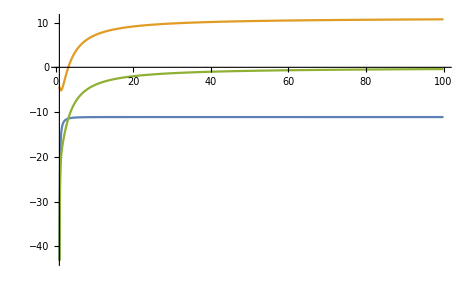

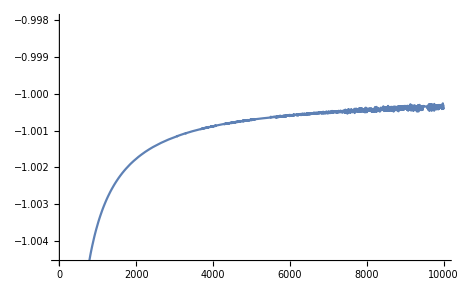

```mathematica
Plot[{t^3 bdVirtualLU[0.32,0.154,0.527,t 0.52,t 0.293,t 0.926,1,0,0,1,1,0,0,-1],t^3 bd4DCTLTD[0.32,0.154,0.527,t 0.52,t 0.293,t 0.926,1,0,0,1,1,0,0,-1],t^3 bdVirtualLU[0.32,0.154,0.527,t 0.52,t 0.293,t 0.926,1,0,0,1,1,0,0,-1]+t^3 bd4DCTLTD[0.32,0.154,0.527,t 0.52,t 0.293,t 0.926,1,0,0,1,1,0,0,-1]},{t,1,100}]


Plot[{(bdVirtualLU[0.32,0.154,0.527,t 0.52,t 0.293,t 0.926,1,0,0,1,1,0,0,-1]/bd4DCTLTD[0.32,0.154,0.527,t 0.52,t 0.293,t 0.926,1,0,0,1,1,0,0,-1])},{t,1,10000}]
```

### Cross section per supergraph

#### Toy model

```mathematica
bubbleSum[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=bdReal[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p2x,p2y,p2z]+bdVirtual[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p2x,p2y,p2z];
```

#### LU

```mathematica
bubLUrep[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_,sigma_,DEBUG_,UV_]:=Module[{vt,rt,sum,c, uvCT=0},
rt=rSolBub[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z];
vt=vSolBub[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z];

c=const[p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]/(Sqrt[Pi]sigma );

If[UV, uvCT=vt^6(Exp[-vt^2/sigma^2])/(vSolBubDiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])bd4DCTLTD[vt*kx,vt*ky,vt*kz,vt*lx,vt*ly,vt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]];

sum=( vt^6(Exp[-vt^2/sigma^2])/(vSolBubDiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])bdVirtualLU[vt*kx,vt*ky,vt*kz,vt*lx,vt*ly,vt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]+rt^6(Exp[-rt^2/sigma^2])/(rSolBubDiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])bdRealLU[rt*kx,rt*ky,rt*kz,rt*lx,rt*ly,rt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]);

If[DEBUG,
Print["virtual: "];
Print[c vt^6(Exp[-vt^2/sigma^2])/(vSolBubDiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])bdVirtualLU[vt*kx,vt*ky,vt*kz,vt*lx,vt*ly,vt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]];
Print["real: "];
Print[c rt^6(Exp[-rt^2/sigma^2])/(rSolBubDiracJ[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])bdRealLU[rt*kx,rt*ky,rt*kz,rt*lx,rt*ly,rt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]];];

c*(sum+uvCT)
];
```

### Tests of LU expression

#### LU expression test

```mathematica
bubLUrep[-0.0201817368890378,0.06211299937499417,0.08989077715277194,-0.5393446629166317,-0.39185683486164874,0,1,0,0,1,1,0,0,-1,2,True,False]
Print["-----------"]
Print["virtual benchmark: "];
Print["-0.0000294636"];
Print["real benchmark: "];
Print["4.001390989976316`"];
```

virtual:

0.-0.0000294636 ⅈ

real:

0.+4.00139 ⅈ

0.+4.00136 ⅈ

-----------

virtual benchmark:

-0.0000294636

real benchmark:

4.001390989976316`

### Tests of Toy model

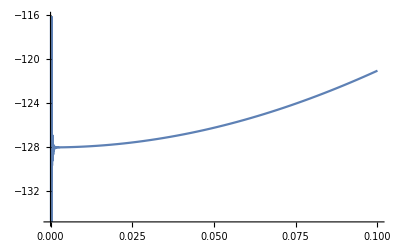

```mathematica
Plot[{bubbleSum[0,eps,1,0,0,0.5,1,0,0,1,0,0,-1],bdVirtual[0,eps,1,0,0,0.5,0,0,0,1,1], bdReal[0,eps,1,0,0,0.5,0,0,0,1,1]},{eps,0,0.1}]
```

## -Graphics-

### Normalisation

```mathematica
const[p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=0.389379*10^(9)*(gs^2 ge^4 Qd^2 Qe^2(-2 Pi I)^3/(4(2 Pi)^8  SP[{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z},{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]^3))/.{ge->N[Sqrt[4π 1/(132.507`16)]], gs->N[Sqrt[4π 0.118`16]],Qe->1,Qd->1/3}
```

### Causal flow

#### Flow solutions

```mathematica
usualtSTch[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=(p10+p20)/(norm[{0,kx,ky,kz}+{0,lx,ly,lz}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}]+norm[{0,kx,ky,kz}]-norm[{0,lx,ly,lz}])

weirdtSTch[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=(p10+p20)/(norm[{0,kx,ky,kz}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}]+norm[{0,kx,ky,kz}])
```

#### Dirac delta jacobians

```mathematica
usualDiracJSTch[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=Dot[Grad[norm[{0,sx,sy,sz}+{0,ax,ay,az}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}]+norm[{0,sx,sy,sz}]-norm[{0,ax,ay,az}],{sx,sy,sz,ax,ay,az}],{sx,sy,sz,ax,ay,az}]/.{sx->kx,sy->ky,sz->kz,ax->lx,ay->ly,az->lz};

weirdDiracJSTch[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=Dot[Grad[norm[{0,sx,sy,sz}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}]+norm[{0,sx,sy,sz}],{sx,sy,sz,ax,ay,az}],{sx,sy,sz,ax,ay,az}]/.{sx->kx,sy->ky,sz->kz,ax->lx,ay->ly,az->lz};
```

### Usual cut

Numerator eliminates a singularity

```mathematica
usualSTCut[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=((twoV2Numerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2k0 2(k0+l0+p10+p20)2l0]SP[{k0,kx,ky,kz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z},{k0,kx,ky,kz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]SP[{l0,lx,ly,lz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z},{l0,lx,ly,lz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]))/.{p20->-p10-k0-l0+norm[{0,kx,ky,kz}+{0,lx,ly,lz}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}]}/.{l0->norm[{0,lx,ly,lz}]}/.{k0->-norm[{0,kx,ky,kz}]})

usualSTCut[0,0.00000001,-0.5,0,0,1,1,0,0,1,0,0,-1];
```

```mathematica
usualSTCutLU[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=((twoV2Numerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2k0 2(k0+l0+p10+p20)2l0]SP[{k0,kx,ky,kz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z},{k0,kx,ky,kz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]SP[{l0,lx,ly,lz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z},{l0,lx,ly,lz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]))/.{l0->norm[{0,lx,ly,lz}]}/.{k0->-norm[{0,kx,ky,kz}]})
```

### Weird cut 1

This one is a diagram without support, and should not be included ultimately. Indeed, there is no such singularity in the original diagram (once energy conservation is applied)

```mathematica
weirdSTCut1[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=((twoV2Numerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2k0 2(k0+p10+p20)2(k0+l0+p10+p20)]SP[{l0,lx,ly,lz},{l0,lx,ly,lz}]SP[{l0,lx,ly,lz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z},{l0,lx,ly,lz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]))/.{l0->-k0-p10-p20+norm[{0,kx,ky,kz}+{0,lx,ly,lz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]}/.{p20->-p10-k0-norm[{0,kx,ky,kz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]}/.{k0->-norm[{0,kx,ky,kz}]})

weirdSTCut1[kx,ky,kz,lx,ly,lz,0,0,0,1,1];
```

```mathematica
weirdSTCut1LU[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=((twoV2Numerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2k0 2(k0+p10+p20)2(k0+l0+p10+p20)]SP[{l0,lx,ly,lz},{l0,lx,ly,lz}]SP[{l0,lx,ly,lz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z},{l0,lx,ly,lz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]))/.{l0->-k0-p10-p20+norm[{0,kx,ky,kz}+{0,lx,ly,lz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]}/.{k0->-norm[{0,kx,ky,kz}]})
```

#### Numerator cancellation

It seems that, even without considering the fact that the singularity has no support, it wouldn' t be there to begin with, because the numerator exactly vanishes at the location of the singularity

```mathematica
funct[x_,y_]:=Simplify[(twoV2Numerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/.{p20->-p10-k0-l0+norm[{0,kx,ky,kz}+{0,lx,ly,lz}+{0,p1x,p1y,p1z}+{0,p2x,p2y,p2z}]}/.{l0->norm[{0,lx,ly,lz}]}/.{k0->-norm[{0,kx,ky,kz}]})/.{p10->1,p1x->0,p1y->0,p1z->1,p2x->0,p2y->0,p2z->-1,kx->0,ky->0,kz->-x,lx->0,ly->0,lz->y}];

funct[0.5,1]
funct[-0.5,1]
```

### Weird cut 2

This is the true and unique ISR singularity

```mathematica
weirdSTCut2[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=((twoV2Numerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2 l0 2 (k0+p10+p20) 2 k0]SP[{k0,kx,ky,kz}+{l0,lx,ly,lz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z},{k0,kx,ky,kz}+{l0,lx,ly,lz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}] SP[{l0,lx,ly,lz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z},{l0,lx,ly,lz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]))/.{p20->-p10-k0+norm[{0,kx,ky,kz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]}/.{k0->-norm[{0,kx,ky,kz}]}/.{l0->norm[{0,lx,ly,lz}]})

v2WeirdCut2[kx,ky,kz,lx,ly,lz,0,0,0,1,1];
```

```mathematica
weirdSTCut2LU[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_]:=((twoV2Numerator[{k0,kx,ky,kz},{l0,lx,ly,lz},{p10,p1x,p1y,p1z},{p20,p2x,p2y,p2z}]/(Abs[2 l0 2 (k0+p10+p20) 2 k0]SP[{k0,kx,ky,kz}+{l0,lx,ly,lz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z},{k0,kx,ky,kz}+{l0,lx,ly,lz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}] SP[{l0,lx,ly,lz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z},{l0,lx,ly,lz}+{p10,p1x,p1y,p1z}+{p20,p2x,p2y,p2z}]))/.{k0->-norm[{0,kx,ky,kz}]}/.{l0->norm[{0,lx,ly,lz}]})
```

### Cross section per supergraph

#### Toy model

```mathematica
stChannelSum[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p2x_,p2y_,p2z_]:=v2UsualCut[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p2x,p2y,p2z]+v2WeirdCut1[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p2x,p2y,p2z]+v2WeirdCut2[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p2x,p2y,p2z]
```

#### LU

```mathematica
stChannelSumLU[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_,sigma_,DEBUG_]:=Module[{vt,rt,sum,c},
vt=usualtSTch[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z];
rt=weirdtSTch[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z];

(*Print[vt];
Print[rt1];
Print[rt2];*)
c=I*const[p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]/(Sqrt[Pi]sigma );

sum=(vt^6(Exp[-vt^2/sigma^2])/(usualDiracJSTch[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])usualSTCutLU[vt*kx,vt*ky,vt*kz,vt*lx,vt*ly,vt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]+rt^6(Exp[-rt^2/sigma^2])/(weirdDiracJSTch[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])weirdSTCut2LU[rt*kx,rt*ky,rt*kz,rt*lx,rt*ly,rt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]
);

If[DEBUG,
Print["usual: "];
];

c*sum
];
```

```mathematica
stChannelSumLU[1,2,3,4,5,6,1,0,0,1,1,0,0,-1,1,False]
```

-0.000055156+0. ⅈ

#### LU single integrands

```mathematica
usualSTChannelSumLU[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_,sigma_,DEBUG_]:=Module[{vt,sum,c},
vt=usualtSTch[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z];

c=I*const[p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]/(Sqrt[Pi]sigma );

sum=(vt^6(Exp[-vt^2/sigma^2])/(usualDiracJSTch[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])usualSTCutLU[vt*kx,vt*ky,vt*kz,vt*lx,vt*ly,vt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]
);

c*sum
];


weirdSTChannelSumLU[kx_,ky_,kz_,lx_,ly_,lz_,p10_,p1x_,p1y_,p1z_,p20_,p2x_,p2y_,p2z_,sigma_,DEBUG_]:=Module[{rt,sum,c},
rt=weirdtSTch[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z];

c=I*const[p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]/(Sqrt[Pi]sigma );

sum=(rt^6(Exp[-rt^2/sigma^2])/(weirdDiracJSTch[kx,ky,kz,lx,ly,lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z])weirdSTCut2LU[rt*kx,rt*ky,rt*kz,rt*lx,rt*ly,rt*lz,p10,p1x,p1y,p1z,p20,p2x,p2y,p2z]
);

c*sum
];
```

### Tests of LU expression

#### IR limits

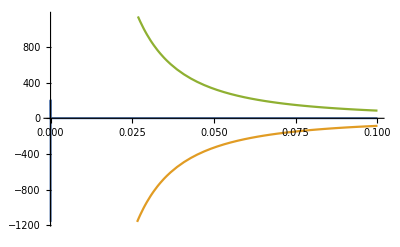

```mathematica
Plot[{stChannelSumLU[0,eps,0.5,0,0,1,1,0,0,1,1,0,0,-1,1,False],usualSTChannelSumLU[0,eps,0.5,0,0,1,1,0,0,1,1,0,0,-1,1,False],weirdSTChannelSumLU[0,eps,0.5,0,0,1,1,0,0,1,1,0,0,-1,1,False]},{eps,0,0.1}]
```

### Tests of Toy model

#### IR limits

Look at Weird Cut 1 cancellation folder for explanation of the absence of the following singularity

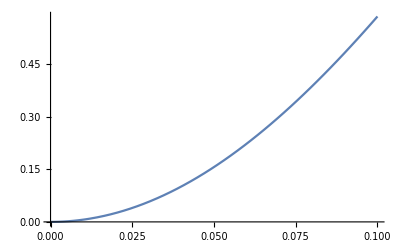

```mathematica
Plot[{usualSTCut[0,eps,-0.5,0,0,1,1,0,0,1,0,0,-1]+weirdSTCut1[0,eps,-0.5,0,0,1,1,0,0,1,0,0,-1](*, bdReal[0,eps,1,0,0,0.5,0,0,0,1,1]*)},{eps,0,0.1}]
```

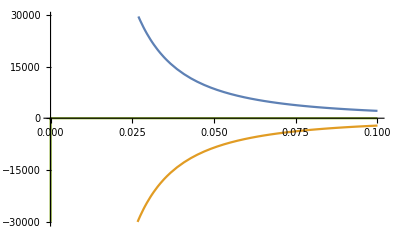

```mathematica
Plot[{usualSTCut[0,eps,0.5,0,0,1,1,0,0,1,0,0,-1],weirdSTCut2[0,eps,0.5,0,0,1,1,0,0,1,0,0,-1],usualSTCut[0,eps,0.5,0,0,1,1,0,0,1,0,0,-1]+weirdSTCut2[0,eps,0.5,0,0,1,1,0,0,1,0,0,-1](*, bdReal[0,eps,1,0,0,0.5,0,0,0,1,1]*)},{eps,0,0.1}]
```

## NLO inclusive d dbar

```mathematica
bubbleResult=176.303
dtResult=445.03
```

176.303

445.03

```mathematica
bubbleResult=Table[NIntegrate[bubLUrep[kx,ky,kz,lx,ly,lz,1,0,0,1,1,0,0,-1,2,False,True],{kx,-Infinity,Infinity},{ky,-Infinity,Infinity},{kz,-Infinity,Infinity},{lx,-Infinity,Infinity},{ly,-Infinity,Infinity},{lz,-Infinity,Infinity},Method->"AdaptiveMonteCarlo",PrecisionGoal->5,MaxPoints-> i*1000000,MaxRecursion->1000],{i,1,10}]
```

```mathematica
dtResult=NIntegrate[dtLUrep[kx,ky,kz,lx,ly,lz,1,0,0,1,1,0,0,-1,2,False,True],{kx,-Infinity,Infinity},{ky,-Infinity,Infinity},{kz,-Infinity,Infinity},{lx,-Infinity,Infinity},{ly,-Infinity,Infinity},{lz,-Infinity,Infinity},Method->"AdaptiveMonteCarlo",PrecisionGoal->5,MaxPoints-> 100000000,MaxRecursion->1000](*,{i,1,10}]*)
```

NIntegrate::maxp: The integral failed to converge after 100000100 integrand evaluations. NIntegrate obtained 0.+445.03 ⅈ and 0.258656 for the integral and error estimates.

0.+445.03 ⅈ

```mathematica
bubbleCTResult=0.118`16/(3*Pi)*loResult
```

96.9146

```mathematica
dtResult-(bubbleResult-bubbleCTResult)*2
```

286.253